```mathematica
BigData = Import[
FileNameJoin[{NotebookDirectory[], "Chip1.ply"}],"VertexData"];
Length[BigData]
```

671123

```mathematica
data = BigData[[1;;-1;;50]]; (* This takes every other 50 pts*)
Length[data]
RoundingValue=.1;
dataDim[1] = Sort[DeleteDuplicates[Table[Round[data[[i]][[1]],RoundingValue],{i,1,Length[data]}]]];
dataDim[2]=  Sort[DeleteDuplicates[Table[Round[data[[i]][[2]],RoundingValue],{i,1,Length[data]}]], Greater];
dataDim[3] =  Sort[DeleteDuplicates[Table[Round[data[[i]][[3]],RoundingValue],{i,1,Length[data]}]]];
Table[{Max[dataDim[i]], Min[dataDim[i]]},{i,1,3}]
```

13423

{{37.,-1.1},{-8.7,-64.},{31.7,13.1}}

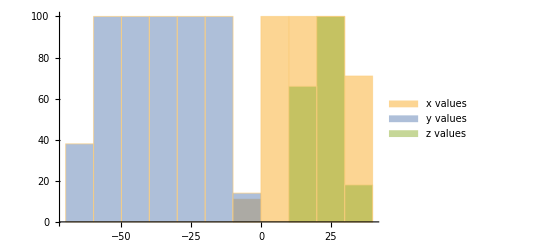

```mathematica
Histogram[{dataDim[1], dataDim[2], dataDim[3]}, ChartLegends->{"x values","y values","z values"}]
```

-Graphics3D-

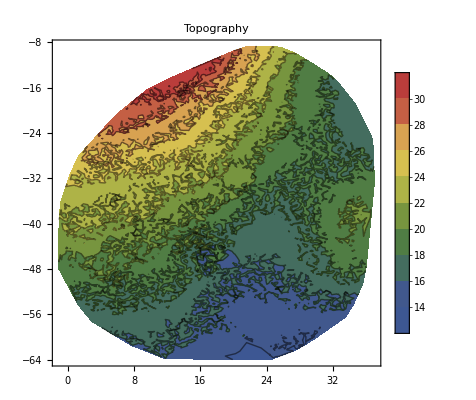

```mathematica
ListPlot3D[data, ColorFunction->"Rainbow", BoxRatios->Automatic,Mesh->None, PlotStyle->{Thickness[50]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->100],PlotLabel->"3D Potato Chip",AxesLabel->{x,y,z},LabelStyle->Bold]

ListContourPlot[data,Mesh->10,PlotRange->All,InterpolationOrder->3,PlotLegends->Automatic, ColorFunction->"DarkRainbow", PlotLabel->"Topography",LabelStyle->Bold]
```

```mathematica
Chip=Interpolation[data, InterpolationOrder->1,"ExtrapolationHandler"->{0&,"WarningMessage"->False}]; (*This is a function to create an interpolation of dataset*)
```

```mathematica
Chip[10,-50];
Chip[0,-60];
```

```mathematica
Chiper[i_,j_]:=Which[
i==1==j,1,
(* I am going to have a 0 for the first entries, but it is also possible to run with the corrodrinates*)
j==1,0 (* dataDim[1][[i-1]] to put in the values of x *),
i==1, 0  (* dataDim[2][[j-1]] to put in the values of y *),
True,Round[Chip[dataDim[1][[i-1]], dataDim[2][[j-1]]],RoundingValue]
]
```

```mathematica
Chiper[1,1];
Chiper[2,1];
Chiper[1,2];
Chiper[2,2];
dataDim[1];
dataDim[2];
Chiper[100,100];
```

```mathematica
MatrixChip=Table[Chiper[i,j], {j,1,Length[dataDim[2]]+1},{i,1,Length[dataDim[1]]+1}];
MatrixChip//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.1 | 27. | 26.9 | 26.8 | 26.7 | 26.6 | 26.5 | 26.4 | 26.3 | 26.2 | 26.1 | 26. | 25.9 | 25.8 | 25.7 | 25.6 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25.1 | 24.9 | 24.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.2 | 27.1 | 27.1 | 27. | 26.9 | 26.7 | 26.5 | 26.3 | 26.2 | 26.1 | 26.1 | 26.1 | 26.1 | 26. | 25.9 | 25.9 | 25.8 | 25.6 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 25. | 25. | 25. | 24.9 | 24.8 | 24.6 | 24.5 | 24.3 | 24.2 | 24. | 23.9 | 23.7 | 23.6 | 23.4 | 23.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.3 | 27.5 | 27.1 | 27.1 | 27.1 | 27. | 27. | 26.9 | 26.6 | 26.4 | 26.3 | 26.3 | 26.3 | 26.3 | 26.2 | 26. | 25.8 | 25.8 | 25.8 | 25.7 | 25.6 | 25.5 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.7 | 24.7 | 24.6 | 24.5 | 24.4 | 24.2 | 24. | 23.9 | 23.7 | 23.5 | 23.4 | 23.3 | 23.5 | 23.4 | 23.2 | 23.1 | 22.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.7 | 27.5 | 27.1 | 27.1 | 27.2 | 27.1 | 27. | 27. | 26.9 | 26.8 | 26.6 | 26.4 | 26.4 | 26.4 | 26.3 | 26.1 | 26. | 25.8 | 25.6 | 25.7 | 25.7 | 25.6 | 25.5 | 25.4 | 25.3 | 25.1 | 25. | 24.9 | 24.8 | 24.8 | 24.7 | 24.6 | 24.5 | 24.3 | 24.2 | 24. | 23.8 | 23.6 | 23.4 | 23.2 | 23.4 | 23.5 | 23.5 | 23.4 | 23.3 | 23.1 | 23. | 22.9 | 22.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.8 | 27.8 | 27.5 | 27.3 | 27. | 27. | 27.2 | 27.1 | 27. | 26.9 | 26.8 | 26.7 | 26.7 | 26.5 | 26.5 | 26.4 | 26.3 | 26.1 | 25.9 | 25.7 | 25.6 | 25.5 | 25.6 | 25.6 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.3 | 24. | 23.9 | 23.7 | 23.5 | 23.3 | 23.3 | 23.4 | 23.6 | 23.6 | 23.5 | 23.3 | 23.2 | 23.1 | 23. | 22.8 | 22.8 | 22.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 27.9 | 28.1 | 27.8 | 27.7 | 27.6 | 27.4 | 27. | 26.8 | 27. | 26.9 | 26.8 | 26.7 | 26.7 | 26.7 | 26.7 | 26.7 | 26.5 | 26.4 | 26.2 | 26. | 25.9 | 25.7 | 25.6 | 25.4 | 25.4 | 25.4 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.3 | 23.9 | 23.7 | 23.5 | 23.3 | 23.2 | 23.3 | 23.4 | 23.6 | 23.7 | 23.6 | 23.4 | 23.3 | 23.2 | 23.1 | 22.9 | 22.8 | 22.7 | 22.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28. | 28.3 | 28.2 | 28.1 | 28. | 27.9 | 27.8 | 27.4 | 27.2 | 26.9 | 26.7 | 26.8 | 26.7 | 26.6 | 26.6 | 26.6 | 26.7 | 26.5 | 26.6 | 26.5 | 26.3 | 26.2 | 26. | 25.8 | 25.7 | 25.4 | 25.3 | 25.3 | 25.4 | 25.3 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.3 | 23.9 | 23.6 | 23.4 | 23.3 | 23.1 | 23.3 | 23.4 | 23.6 | 23.7 | 23.6 | 23.5 | 23.4 | 23.3 | 23.2 | 23. | 22.9 | 22.8 | 22.7 | 22.6 | 22.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.2 | 28.5 | 28.5 | 28.4 | 28.3 | 28.2 | 28. | 27.9 | 27.8 | 27.7 | 27.5 | 27.1 | 26.6 | 26.6 | 26.5 | 26.4 | 26.5 | 26.6 | 26.7 | 26.7 | 26.2 | 26.2 | 26.3 | 26.3 | 26.1 | 26. | 25.8 | 25.5 | 25.2 | 25.2 | 25.2 | 24.9 | 25.2 | 25.1 | 25. | 24.8 | 24.7 | 24.6 | 24.7 | 24.5 | 24.5 | 24.3 | 23.9 | 23.5 | 23.3 | 23.2 | 23.1 | 23.3 | 23.4 | 23.6 | 23.7 | 23.7 | 23.6 | 23.5 | 23.4 | 23.3 | 23.1 | 22.9 | 22.9 | 22.8 | 22.7 | 22.6 | 22.6 | 22.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.2 | 28.3 | 28.4 | 28.5 | 28.6 | 28.2 | 28. | 27.9 | 27.8 | 27.9 | 27.6 | 27.3 | 27.3 | 27.1 | 26.8 | 26.4 | 26.4 | 26.4 | 26.5 | 26.6 | 26.7 | 26.7 | 25.8 | 25.8 | 25.8 | 25.9 | 26. | 26. | 25.9 | 25.6 | 25.3 | 25.1 | 24.9 | 24.7 | 24.8 | 24.7 | 24.6 | 24.6 | 24.6 | 24.8 | 24.6 | 24.4 | 24.3 | 24.2 | 23.8 | 23.5 | 23.3 | 23.2 | 23.2 | 23.3 | 23.4 | 23.4 | 23.4 | 23.3 | 23.2 | 23.1 | 23.1 | 23.2 | 23.1 | 22.5 | 22.5 | 22.7 | 22.8 | 22.7 | 22.6 | 22.5 | 22.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.1 | 28.1 | 28.2 | 28.3 | 28.3 | 28.4 | 28.5 | 28.1 | 27.8 | 27.7 | 27.5 | 27.8 | 27.3 | 27.7 | 26.8 | 26.7 | 26.6 | 26.4 | 26.3 | 26.4 | 26.5 | 26.6 | 26.7 | 26.8 | 25.9 | 25.7 | 25.8 | 25.9 | 26. | 26.1 | 25.8 | 25.9 | 25.5 | 25.1 | 25. | 24.9 | 24.5 | 24.5 | 24.5 | 24.5 | 24.8 | 24.8 | 24.5 | 24.2 | 24.2 | 24.1 | 23.8 | 23.5 | 23.4 | 23.2 | 23.2 | 23. | 23. | 23. | 23. | 22.9 | 22.9 | 22.9 | 23. | 23.1 | 23.1 | 22.4 | 22.2 | 22.4 | 22.6 | 22.6 | 22.6 | 22.6 | 22.5 | 22.4 | 22.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.5 | 28.3 | 28.1 | 28.1 | 28.2 | 28.3 | 28.4 | 28.4 | 28.5 | 28.2 | 27.5 | 27.4 | 28.1 | 27.6 | 27.1 | 27.3 | 27.1 | 26.9 | 26.7 | 26.5 | 26.4 | 26.6 | 26.7 | 26.8 | 26.9 | 26.8 | 26. | 25.9 | 25.9 | 26. | 26.1 | 26.1 | 25.8 | 25.4 | 25.8 | 25.6 | 24.7 | 24.6 | 24.5 | 24.5 | 24.5 | 24.8 | 25. | 24.7 | 24.4 | 24.1 | 24. | 24. | 23.7 | 23.5 | 23.4 | 23.8 | 23.8 | 23.6 | 23.2 | 22.8 | 22.6 | 22.6 | 22.7 | 22.9 | 23. | 23.1 | 23.1 | 22.2 | 22. | 22.1 | 22.3 | 22.4 | 22.4 | 22.4 | 22.4 | 22.4 | 22.4 | 22.4 | 22.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.8 | 28.4 | 28.2 | 28. | 28.1 | 28.3 | 28.4 | 28.4 | 28.5 | 28.6 | 28. | 27.5 | 27.8 | 27.9 | 27.6 | 27.4 | 27.3 | 27.4 | 27.2 | 26.9 | 26.5 | 26.2 | 26.8 | 26.9 | 27. | 26.9 | 26.7 | 26.2 | 26.1 | 26. | 26.1 | 26.2 | 26.1 | 25.7 | 25.3 | 25. | 24.8 | 24.7 | 24.6 | 24.5 | 24.4 | 24.7 | 25. | 24.9 | 24.6 | 24.3 | 24. | 23.8 | 23.8 | 23.7 | 23.5 | 23.4 | 23.2 | 23.2 | 23. | 22.9 | 22.8 | 22.6 | 22.6 | 22.7 | 22.8 | 22.9 | 23. | 23. | 22.5 | 22.3 | 22.1 | 22. | 22.2 | 22.2 | 22.2 | 22.3 | 22.3 | 22.3 | 22.3 | 22.3 | 22.3 | 22.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.8 | 29. | 28.6 | 28.4 | 28.2 | 28. | 28.1 | 28.3 | 28.4 | 28.5 | 28.6 | 28.3 | 27.7 | 27.4 | 27.6 | 28.1 | 27.9 | 27.8 | 27.7 | 27.6 | 27.3 | 26.9 | 26.5 | 26. | 26.7 | 27.1 | 27. | 26.8 | 26.7 | 26.4 | 26.3 | 26.2 | 26.2 | 26.3 | 26. | 25.7 | 25.5 | 25.4 | 24.9 | 24.7 | 24.6 | 24.5 | 24.6 | 25. | 25.2 | 24.9 | 24.7 | 24.4 | 24.1 | 23.7 | 23.7 | 23.6 | 23.5 | 23.3 | 23.3 | 23.4 | 23.3 | 23.2 | 23. | 22.7 | 22.5 | 22.6 | 22.7 | 22.8 | 22.9 | 23. | 22.8 | 22.6 | 22.4 | 22.2 | 22. | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 22.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.4 | 28.9 | 28.8 | 28.5 | 28.3 | 28.1 | 28. | 28.1 | 28.3 | 28.4 | 28.5 | 28.7 | 28.5 | 28.4 | 27.8 | 27.1 | 27.4 | 27.6 | 27.5 | 27.4 | 27.3 | 27.1 | 26.9 | 26.5 | 26.1 | 26.6 | 26.9 | 26.8 | 26.7 | 26.6 | 26.6 | 26.6 | 26.5 | 26.4 | 26.3 | 26.1 | 26. | 25.8 | 25.7 | 25.1 | 24.7 | 24.6 | 24.5 | 24.9 | 25. | 25.1 | 25. | 24.9 | 24.8 | 24.5 | 24.2 | 23.7 | 23.6 | 23.4 | 23.3 | 23.5 | 23.6 | 23.5 | 23.4 | 23.1 | 22.7 | 22.4 | 22.5 | 22.6 | 22.7 | 22.9 | 23. | 22.9 | 22.7 | 22.5 | 22.4 | 22.2 | 22. | 21.6 | 21.4 | 21.5 | 21.6 | 21.7 | 21.8 | 21.9 | 21.9 | 22. | 22. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.2 | 29.1 | 29. | 29.1 | 28.8 | 28.4 | 28.2 | 28. | 28. | 28.2 | 28.3 | 28.5 | 28.6 | 28.7 | 28.5 | 28.3 | 27.6 | 27.2 | 27. | 27.1 | 27. | 26.9 | 26.9 | 26.7 | 26.5 | 26.2 | 26.1 | 26.1 | 26.3 | 26.5 | 26.4 | 26.3 | 26.3 | 26.3 | 26.2 | 26.2 | 26.4 | 26.3 | 26.3 | 26.2 | 26. | 25.4 | 24.8 | 24.6 | 24.7 | 24.8 | 24.9 | 25. | 25. | 24.9 | 24.8 | 24.7 | 24.5 | 24.2 | 23.6 | 23.4 | 23.3 | 23.1 | 23.7 | 23.8 | 23.5 | 23.1 | 22.8 | 22.4 | 22.5 | 22.6 | 22.7 | 22.8 | 22.8 | 22.8 | 22.6 | 22.4 | 22.2 | 22.1 | 21.5 | 21.3 | 21.4 | 21.5 | 21.6 | 21.7 | 21.7 | 21.8 | 21.9 | 21.8 | 21.9 | 21.9 | 21.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28.8 | 29.4 | 29.1 | 29.2 | 29.2 | 29.1 | 28.8 | 28.4 | 28.2 | 28. | 27.9 | 28. | 28.2 | 28.4 | 28.4 | 28.4 | 28.3 | 28. | 27.3 | 27.1 | 27. | 27. | 26.7 | 26.5 | 26.5 | 26.4 | 26.3 | 26.2 | 26.1 | 25.9 | 25.8 | 25.9 | 26.1 | 26. | 25.9 | 25.9 | 25.9 | 26. | 26.4 | 26.4 | 26.3 | 26.2 | 26.1 | 25.6 | 25. | 24.6 | 24.7 | 24.7 | 24.8 | 24.9 | 25. | 24.9 | 24.8 | 24.7 | 24.5 | 24.4 | 24.1 | 23.7 | 23.3 | 23.1 | 22.9 | 23.9 | 23.6 | 23.2 | 22.8 | 22.4 | 22.4 | 22.5 | 22.5 | 22.6 | 22.6 | 22.6 | 22.5 | 22.3 | 22.2 | 21.9 | 21.4 | 21.4 | 21.4 | 21.5 | 21.5 | 21.6 | 21.7 | 21.8 | 21.8 | 21.7 | 21.7 | 21.8 | 21.8 | 21.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.5 | 29.3 | 29.3 | 29.3 | 29.4 | 29.4 | 29.1 | 28.7 | 28.3 | 28.1 | 28. | 27.8 | 27.9 | 28.1 | 28.1 | 28.1 | 28.1 | 28. | 27.8 | 27.2 | 27.1 | 27.2 | 27. | 26.8 | 26.4 | 26.1 | 26.2 | 26.3 | 26.3 | 26. | 25.9 | 25.8 | 25.6 | 25.5 | 25.7 | 25.6 | 25.6 | 25.6 | 25.8 | 26.4 | 26.4 | 26.3 | 26.3 | 26.2 | 25.6 | 24.9 | 25. | 25. | 24.9 | 24.8 | 24.9 | 24.9 | 24.9 | 24.8 | 24.7 | 24.5 | 24.5 | 24.2 | 23.8 | 23.4 | 23.1 | 23. | 23.5 | 23.2 | 22.9 | 22.7 | 22.4 | 22.3 | 22.4 | 22.4 | 22.4 | 22.5 | 22.5 | 22.4 | 22.3 | 22.2 | 21.7 | 21.4 | 21.4 | 21.2 | 21.4 | 21.5 | 21.6 | 21.7 | 21.7 | 21.6 | 21.6 | 21.6 | 21.7 | 21.7 | 21.8 | 21.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.4 | 29.4 | 29.4 | 29.4 | 29.5 | 29.5 | 29.5 | 29.5 | 29.1 | 28.7 | 28.3 | 28.1 | 27.9 | 27.7 | 27.8 | 27.8 | 27.8 | 27.8 | 27.8 | 27.7 | 27.6 | 27.2 | 27.2 | 27.3 | 27.1 | 26.8 | 26.5 | 26.2 | 27. | 27.1 | 26.5 | 26. | 25.9 | 25.8 | 25.6 | 25.5 | 25.4 | 25.3 | 25.3 | 25.4 | 25.7 | 26.3 | 26.4 | 26.3 | 26.1 | 25.8 | 25.4 | 24.6 | 25.2 | 25.4 | 25.3 | 25.3 | 25.2 | 25. | 24.8 | 24.6 | 24.4 | 24.5 | 24.5 | 24.2 | 23.9 | 23.5 | 23.1 | 23. | 23.1 | 22.8 | 22.6 | 22.4 | 22.3 | 22.3 | 22.4 | 22.4 | 22.5 | 22.5 | 22.2 | 22.2 | 22.4 | 22. | 21.7 | 21.3 | 21.4 | 21.1 | 21.3 | 21.5 | 21.6 | 21.7 | 21.6 | 21.4 | 21.4 | 21.5 | 21.5 | 21.6 | 21.7 | 21.6 | 21.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.9 | 29.5 | 29.6 | 29.6 | 29.6 | 29.7 | 29.7 | 29.7 | 29.4 | 29.1 | 28.6 | 28.3 | 28.1 | 27.9 | 27.7 | 27.6 | 27.5 | 27.5 | 27.5 | 27.4 | 27.4 | 27.4 | 27.3 | 27.5 | 27.4 | 27.1 | 26.9 | 26.6 | 26.3 | 26.7 | 27.6 | 27.1 | 26.2 | 25.9 | 25.7 | 25.6 | 25.5 | 25.5 | 25.2 | 25.2 | 25.1 | 25.7 | 26.2 | 26.3 | 25.9 | 25.6 | 25.2 | 24.8 | 24.8 | 25.2 | 25.6 | 25.5 | 25.3 | 25.1 | 24.9 | 24.6 | 24.2 | 24. | 24.4 | 24.4 | 24.1 | 23.8 | 23.5 | 23.1 | 22.9 | 22.9 | 22.7 | 22.5 | 22.4 | 22.3 | 22.3 | 22.4 | 22.5 | 22.5 | 22.5 | 21.9 | 22.2 | 22.2 | 21.9 | 21.6 | 21.2 | 21.4 | 21.2 | 21.1 | 21.5 | 21.6 | 21.5 | 21.4 | 21.3 | 21.3 | 21.4 | 21.4 | 21.5 | 21.5 | 21.6 | 21.5 | 21.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.8 | 29.7 | 29.7 | 29.7 | 29.8 | 29.8 | 29.8 | 29.9 | 29.9 | 29.8 | 29.3 | 28.8 | 28.4 | 28.3 | 28.1 | 27.9 | 27.9 | 27.9 | 27.9 | 27.8 | 27.7 | 27.6 | 27.5 | 27.2 | 27.6 | 27.7 | 27.4 | 27.2 | 27. | 26.6 | 26.2 | 26.4 | 26.7 | 27.4 | 27.3 | 25.9 | 25.7 | 25.6 | 25.8 | 25.6 | 25.2 | 25.1 | 25.3 | 25.8 | 26.4 | 26.3 | 26.2 | 25.9 | 25.5 | 25.1 | 24.6 | 25. | 25.5 | 25.4 | 25.2 | 25. | 24.8 | 24.5 | 24. | 23.7 | 24.3 | 24.2 | 23.9 | 23.7 | 23.4 | 23.1 | 23.1 | 23.2 | 22.8 | 22.5 | 22.3 | 22.2 | 22.2 | 22.3 | 22.4 | 22.5 | 22.3 | 22.3 | 22.2 | 22. | 21.7 | 21.5 | 21.1 | 21.3 | 21.4 | 20.9 | 21.2 | 21.5 | 21.4 | 21.2 | 21.1 | 21.2 | 21.2 | 21.2 | 21.3 | 21.3 | 21.3 | 21.3 | 21.4 | 21.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.1 | 30.2 | 29.8 | 29.8 | 29.9 | 29.9 | 29.9 | 30. | 30. | 29.9 | 29.9 | 29.7 | 29. | 28.6 | 28.4 | 28.2 | 28.1 | 28.1 | 28.2 | 28.3 | 28.2 | 28.1 | 28. | 27.8 | 27.4 | 27.2 | 27.8 | 27.8 | 27.6 | 27.3 | 26.9 | 26.4 | 26.2 | 26.4 | 26.7 | 27. | 27.2 | 26.3 | 25.9 | 26.2 | 25.9 | 25.5 | 25.2 | 25.1 | 25.5 | 26. | 26.4 | 26.3 | 26.2 | 26.1 | 25.8 | 25.4 | 24.9 | 24.8 | 25.2 | 25.4 | 25.1 | 24.9 | 24.7 | 24.4 | 23.9 | 23.6 | 24.1 | 24.1 | 23.8 | 23.5 | 23.2 | 22.9 | 23.4 | 23.4 | 23. | 22.7 | 22.3 | 22.2 | 22.2 | 22.3 | 22.4 | 22.4 | 22.5 | 22.3 | 22. | 21.8 | 21.5 | 21.3 | 21. | 21.3 | 21.6 | 20.8 | 21.1 | 21.2 | 21.1 | 21. | 21. | 20.9 | 20.9 | 20.9 | 21. | 21. | 21. | 21. | 21. | 21.1 | 20.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.1 | 30.1 | 29.9 | 29.9 | 29.9 | 29.9 | 29.9 | 30. | 30. | 29.7 | 29.7 | 29.7 | 29.6 | 29.2 | 28.6 | 28.4 | 28.2 | 28.2 | 28.4 | 28.5 | 28.6 | 28.5 | 28.4 | 28.1 | 27.7 | 27.3 | 27.2 | 27.8 | 28.1 | 27.6 | 27.1 | 26.6 | 26.2 | 26.1 | 26.4 | 26.7 | 26.9 | 26.9 | 26.9 | 26.5 | 26.2 | 25.9 | 25.5 | 25.2 | 25.2 | 25.7 | 26.2 | 26.3 | 26.2 | 26.1 | 26. | 25.9 | 25.7 | 25.3 | 24.6 | 24.9 | 25.2 | 25. | 24.8 | 24.6 | 24.3 | 24. | 23.8 | 24. | 24. | 23.7 | 23.4 | 23.1 | 22.9 | 23.1 | 23.3 | 23.1 | 22.8 | 22.5 | 22.2 | 22.1 | 22.1 | 22.2 | 22.1 | 22. | 22.2 | 22.1 | 21.9 | 21.6 | 21.4 | 21.1 | 21.1 | 21.4 | 21.1 | 20.9 | 20.9 | 20.8 | 20.9 | 21. | 20.9 | 20.8 | 20.7 | 20.7 | 20.7 | 20.7 | 20.7 | 20.7 | 20.7 | 20.8 | 20.8 | 20.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.7 | 30.5 | 30.3 | 30.1 | 30. | 29.9 | 29.9 | 29.9 | 30. | 30. | 30. | 29.5 | 29.5 | 29.5 | 29.4 | 29. | 28.7 | 28.3 | 28.1 | 28.2 | 28.7 | 28.9 | 28.9 | 28.7 | 28.3 | 27.9 | 27.5 | 27.1 | 27.3 | 27.5 | 27.4 | 27.7 | 27.2 | 26.8 | 26.4 | 26.1 | 26.3 | 26.5 | 26.6 | 26.7 | 26.7 | 26.6 | 26.2 | 25.9 | 25.5 | 25.2 | 25.4 | 25.9 | 26.4 | 26.3 | 26.2 | 26.1 | 26. | 25.8 | 25.7 | 25.6 | 24.9 | 24.5 | 24.8 | 24.8 | 24.6 | 24.4 | 24.3 | 24.2 | 24. | 23.9 | 23.9 | 23.6 | 23.4 | 23.1 | 22.8 | 22.6 | 22.8 | 22.6 | 22.5 | 22.2 | 22.1 | 22. | 21.9 | 21.9 | 21.8 | 21.8 | 21.7 | 22. | 22. | 21.8 | 21.5 | 21.3 | 21.3 | 21.3 | 21.4 | 20.7 | 20.7 | 20.8 | 20.9 | 20.9 | 20.8 | 20.7 | 20.6 | 20.5 | 20.4 | 20.4 | 20.4 | 20.4 | 20.4 | 20.4 | 20.5 | 20.6 | 20.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.4 | 30.7 | 30.5 | 30.3 | 30.2 | 30.1 | 30. | 30. | 30. | 30. | 30. | 29.8 | 29.3 | 29.3 | 29.3 | 29.2 | 28.8 | 28.5 | 28.2 | 28.1 | 28.1 | 28.7 | 28.9 | 28.7 | 28.6 | 28.2 | 27.7 | 27.3 | 26.9 | 26.9 | 26.7 | 26.7 | 27.9 | 27.4 | 27. | 26.6 | 26.2 | 26.1 | 26.3 | 26.3 | 26.4 | 26.4 | 26.5 | 26.3 | 26. | 25.6 | 25.3 | 25.2 | 26. | 26.3 | 26.2 | 26.1 | 26. | 25.9 | 25.8 | 25.4 | 25. | 25.3 | 25. | 24.5 | 24.5 | 24.3 | 24.1 | 24.1 | 24.1 | 24.1 | 23.9 | 23.8 | 23.6 | 23.3 | 23.1 | 22.9 | 22.7 | 22.6 | 22.4 | 22.3 | 22.3 | 22.1 | 22. | 21.9 | 21.9 | 21.9 | 22. | 21.9 | 21.8 | 21.7 | 21.9 | 21.6 | 21.5 | 21.5 | 21.5 | 21.3 | 20.6 | 20.7 | 20.8 | 20.9 | 20.8 | 20.7 | 20.6 | 20.5 | 20.4 | 20.3 | 20.3 | 20.2 | 20.2 | 20.1 | 20.1 | 20.1 | 20.2 | 20.3 | 20.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 30.8 | 30.6 | 30.7 | 30.5 | 30.4 | 30.3 | 30.2 | 30.1 | 30.1 | 30. | 30. | 30. | 29.2 | 29.1 | 29.2 | 29.2 | 28.9 | 28.6 | 28.3 | 28.1 | 28. | 27.9 | 28.4 | 28.4 | 28.1 | 28.6 | 28.2 | 27.8 | 27. | 26.9 | 26.7 | 26.6 | 26.6 | 27.5 | 27.6 | 27.2 | 26.9 | 26.4 | 25.9 | 26. | 26.1 | 26.3 | 26.6 | 26.6 | 26.4 | 26.1 | 25.8 | 25.4 | 25. | 25.7 | 26.2 | 26.2 | 26.1 | 25.9 | 25.7 | 25.1 | 24.7 | 24.6 | 25.1 | 24.8 | 24.6 | 24.3 | 24.1 | 23.9 | 23.9 | 23.9 | 23.9 | 23.9 | 23.8 | 23.6 | 23.4 | 23.2 | 23. | 22.7 | 22.9 | 22.3 | 22.4 | 22.7 | 22.4 | 22.1 | 22. | 22. | 22.1 | 22.1 | 22.1 | 22. | 21.9 | 21.8 | 21.7 | 21.6 | 21.4 | 21.1 | 20.9 | 20.6 | 20.6 | 20.7 | 20.8 | 20.8 | 20.7 | 20.6 | 20.5 | 20.3 | 20.2 | 20.3 | 20.2 | 20.1 | 20.1 | 20. | 20. | 20. | 20. | 20. | 20.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.4 | 30.8 | 30.6 | 30.4 | 30.6 | 30.7 | 30.6 | 30.5 | 30.4 | 30.3 | 30.2 | 30.2 | 30.1 | 30.1 | 30.1 | 29. | 29. | 29. | 29. | 28.7 | 28.4 | 28.2 | 28.1 | 27.9 | 27.7 | 28.1 | 27.9 | 27.6 | 28.1 | 27.4 | 27. | 27.1 | 27.1 | 26.7 | 26.6 | 26.6 | 27.4 | 27.4 | 27.5 | 27.1 | 26.6 | 26. | 26. | 26.4 | 26.6 | 26.7 | 26.6 | 26.6 | 26.3 | 26. | 25.6 | 25.2 | 25.2 | 25.6 | 25.9 | 26. | 25.7 | 25.6 | 25.5 | 25.3 | 25.2 | 24.9 | 24.6 | 24.3 | 24.1 | 23.9 | 23.7 | 23.7 | 23.7 | 23.8 | 23.9 | 23.7 | 23.7 | 23.5 | 23.2 | 23. | 22.5 | 23.1 | 22.7 | 22.4 | 23.1 | 22.8 | 22.3 | 22.2 | 22.2 | 22.2 | 22.3 | 22.4 | 22.2 | 22.1 | 22. | 21.7 | 21.6 | 21.3 | 21. | 20.6 | 20.5 | 20.6 | 20.7 | 20.8 | 20.7 | 20.6 | 20.5 | 20.4 | 20.2 | 20.1 | 20.4 | 20.2 | 20. | 20. | 19.9 | 19.9 | 19.9 | 19.9 | 19.9 | 19.8 | 19.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 30.7 | 30.4 | 30.2 | 30.4 | 30.6 | 30.7 | 30.6 | 30.5 | 30.4 | 30.4 | 30.3 | 30.2 | 30.2 | 29.8 | 29.3 | 28.9 | 28.8 | 28.8 | 28.9 | 28.5 | 28.3 | 28.2 | 28. | 27.8 | 27.6 | 27.6 | 27.4 | 27.2 | 27.1 | 27.2 | 27.3 | 27.4 | 27.2 | 26.9 | 26.6 | 26.6 | 27. | 27. | 27.1 | 27.2 | 26.7 | 26.4 | 26.3 | 26.3 | 26.7 | 26.7 | 26.7 | 26.6 | 26.5 | 26.1 | 25.7 | 25. | 25.1 | 25.4 | 25.8 | 25.9 | 25.7 | 25.6 | 25.4 | 25.3 | 25.1 | 24.7 | 24.3 | 24. | 23.8 | 23.7 | 23.5 | 23.6 | 23.7 | 23.8 | 23.8 | 23.5 | 23.4 | 23.5 | 23.3 | 23.1 | 22.8 | 22.4 | 22.9 | 22.3 | 22.6 | 22.9 | 22.4 | 22.4 | 22.4 | 22.5 | 22.5 | 22.5 | 22.4 | 22.1 | 21.9 | 21.7 | 21.5 | 21.4 | 21.1 | 20.9 | 20.8 | 20.7 | 20.7 | 20.8 | 20.6 | 20.5 | 20.4 | 20.2 | 20.1 | 20.1 | 20.4 | 20.4 | 20.1 | 19.9 | 19.8 | 19.8 | 19.8 | 19.8 | 19.8 | 19.8 | 19.7 | 19.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30. | 30.9 | 30.6 | 30.3 | 30.1 | 30.2 | 30.3 | 30.5 | 30.6 | 30.6 | 30.5 | 30.4 | 30.4 | 30.3 | 30.3 | 29.9 | 29.6 | 29.3 | 28.9 | 28.8 | 28.7 | 28.7 | 28.4 | 28.3 | 28.1 | 27.9 | 27.8 | 27.6 | 27.4 | 28.1 | 27.2 | 27.1 | 27.2 | 27.6 | 27.7 | 27.4 | 27. | 26.7 | 26.6 | 26.7 | 27. | 27.3 | 27.2 | 26.8 | 26.7 | 26.7 | 26.7 | 26.6 | 26.7 | 26.7 | 26.6 | 26.5 | 25.9 | 25.3 | 25. | 25.1 | 25.4 | 25.7 | 25.8 | 25.7 | 25.5 | 25.3 | 25.2 | 25. | 24.6 | 24.1 | 23.7 | 23.6 | 23.5 | 23.4 | 23.6 | 23.7 | 23.8 | 23.7 | 23.4 | 23.1 | 23.2 | 23.3 | 22.5 | 22.7 | 22.9 | 23.1 | 22.8 | 22. | 23. | 22.6 | 22.6 | 22.7 | 22.7 | 22.6 | 22.4 | 22.3 | 22. | 21.8 | 21.6 | 21.5 | 21.4 | 21.2 | 21.1 | 21. | 20.9 | 20.8 | 20.6 | 20.5 | 20.3 | 20.2 | 20. | 20. | 20.3 | 20.6 | 20.5 | 20.4 | 20.3 | 19.8 | 19.8 | 19.7 | 19.7 | 19.7 | 19.7 | 19.6 | 19.6 | 19.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 30.7 | 30.6 | 30.5 | 30.4 | 30.1 | 30. | 30.1 | 30.2 | 30.3 | 30.3 | 30.4 | 30.4 | 30.3 | 30.3 | 30.2 | 29.9 | 29.6 | 29.2 | 28.8 | 28.7 | 28.6 | 28.5 | 28.4 | 28.2 | 28. | 27.9 | 28.2 | 28.1 | 27.7 | 28.8 | 28.2 | 27.3 | 27.2 | 27.9 | 27.9 | 27.5 | 27.2 | 26.9 | 26.6 | 27. | 27.3 | 27.5 | 27.2 | 27.1 | 27. | 27. | 26.9 | 26.8 | 26.5 | 26.2 | 26. | 25.9 | 25.5 | 25.1 | 25. | 25.1 | 25.4 | 25.6 | 25.6 | 25.6 | 25.4 | 25.3 | 25.1 | 24.9 | 24.4 | 23.9 | 23.7 | 23.6 | 23.5 | 23.4 | 23.6 | 23.6 | 23.5 | 23.5 | 23.2 | 23. | 22.9 | 22.6 | 22.5 | 22.6 | 22.8 | 23. | 22.9 | 22.4 | 22.6 | 22.9 | 22.8 | 22.7 | 22.6 | 22.4 | 22.2 | 22.1 | 22. | 21.7 | 21.6 | 21.5 | 21.4 | 21.2 | 21.1 | 20.9 | 20.7 | 20.6 | 20.4 | 20.2 | 20.1 | 20. | 20. | 20. | 20.3 | 20.7 | 20.4 | 20. | 20.3 | 20. | 19.9 | 19.9 | 19.8 | 19.7 | 19.6 | 19.5 | 19.5 | 19.5 | 19.6 | 19.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.5 | 31. | 30.9 | 30.9 | 30.8 | 30.7 | 30.6 | 30.1 | 29.7 | 29.8 | 29.8 | 29.9 | 30. | 30.1 | 30.1 | 30.1 | 30.2 | 30.1 | 29.9 | 29.5 | 29.1 | 28.7 | 28.6 | 28.5 | 28.4 | 28.2 | 28.1 | 27.9 | 28. | 28.5 | 28.6 | 28.4 | 28.8 | 28.1 | 27.5 | 27.2 | 27.9 | 28. | 27.8 | 27.6 | 27.2 | 26.8 | 27.2 | 27.5 | 27.1 | 26.9 | 27.2 | 27.1 | 27. | 26.9 | 26.6 | 26.3 | 26. | 25.7 | 25.4 | 25.2 | 25.1 | 25. | 25.1 | 25.3 | 25.4 | 25.5 | 25.4 | 25.3 | 25.2 | 25. | 24.8 | 24.3 | 24. | 23.8 | 23.6 | 23.5 | 23.4 | 23.4 | 23.4 | 23.3 | 23.3 | 23.1 | 22.8 | 23.5 | 22.8 | 22.5 | 22.6 | 22.7 | 22.9 | 23. | 22.8 | 22.9 | 22.8 | 22.7 | 22.5 | 22.3 | 22.1 | 21.9 | 21.8 | 21.8 | 21.7 | 21.6 | 21.5 | 21.4 | 21.2 | 21.1 | 20.9 | 20.7 | 20.5 | 20.3 | 20.2 | 20.1 | 20. | 19.9 | 20. | 20.3 | 20. | 19.7 | 19.8 | 20.3 | 20.1 | 20. | 20. | 19.8 | 19.6 | 19.5 | 19.4 | 19.4 | 19.5 | 19.5 | 19.5 | 19.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 29.7 | 31. | 31.1 | 31.1 | 31.1 | 31.1 | 31. | 30.9 | 30.6 | 30.2 | 29.9 | 29.6 | 29.5 | 29.6 | 29.7 | 29.7 | 29.8 | 29.8 | 29.8 | 29.9 | 30. | 29.9 | 29.8 | 29.1 | 28.8 | 28.5 | 28.3 | 28.1 | 28. | 27.8 | 28. | 28.5 | 28.9 | 29. | 28.7 | 28. | 27.3 | 27.4 | 27.8 | 27.7 | 27.7 | 27.8 | 27.4 | 27. | 27.3 | 27.3 | 26.3 | 27.5 | 27.3 | 27.1 | 26.9 | 26.6 | 26.4 | 26.1 | 25.8 | 25.5 | 25.3 | 25.4 | 25.2 | 25. | 25.1 | 25.2 | 25.3 | 25.3 | 25.3 | 25.2 | 25.1 | 24.9 | 24.7 | 24.2 | 24.2 | 24.1 | 23.9 | 23.7 | 23.8 | 23.3 | 23.1 | 23.1 | 23.1 | 22.9 | 22.8 | 23. | 23.4 | 22.4 | 22.6 | 22.7 | 22.8 | 22.9 | 22.9 | 22.8 | 22.7 | 22.5 | 22.3 | 22.1 | 21.9 | 21.7 | 21.6 | 21.5 | 21.4 | 21.4 | 21.5 | 21.4 | 21.2 | 21.1 | 20.9 | 20.7 | 20.5 | 20.4 | 20.2 | 20.1 | 20. | 19.9 | 19.9 | 20. | 20.1 | 20.2 | 20.3 | 20.3 | 20.2 | 20.1 | 19.9 | 19.7 | 19.5 | 19.4 | 19.3 | 19.3 | 19.4 | 19.4 | 19.5 | 19.4 | 19.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31. | 31.1 | 31.2 | 31.2 | 31.1 | 31.1 | 31.1 | 31.1 | 30.8 | 30.4 | 30. | 29.8 | 29.5 | 29.3 | 29.3 | 29.4 | 29.4 | 29.5 | 29.7 | 29.9 | 30. | 29.9 | 29.9 | 29.8 | 29.6 | 29.3 | 29. | 28.7 | 28.3 | 28. | 27.7 | 27.6 | 27.6 | 27.8 | 27.5 | 27.8 | 27.2 | 27.3 | 27.2 | 27.1 | 27.2 | 27.6 | 27.6 | 27.2 | 27.5 | 26.7 | 26.8 | 26.9 | 27.4 | 27.1 | 26.7 | 26.4 | 26.1 | 25.9 | 25.6 | 25.3 | 25.5 | 25.6 | 25.6 | 25.2 | 24.9 | 25. | 25.1 | 25.2 | 25.2 | 25.1 | 25. | 24.9 | 24.5 | 24.4 | 24.3 | 24.3 | 24.1 | 24.1 | 23.8 | 23.7 | 23.4 | 23.2 | 22.9 | 23.5 | 23.3 | 23.1 | 23.2 | 22.4 | 22.5 | 22.5 | 22.6 | 22.7 | 22.7 | 22.7 | 22.6 | 22.4 | 22.1 | 21.8 | 21.6 | 21.4 | 21.3 | 21.2 | 21.1 | 21. | 21.1 | 21.3 | 21.2 | 21.1 | 20.9 | 20.7 | 20.7 | 20.6 | 20.3 | 20. | 20. | 19.9 | 20.1 | 20.2 | 20.3 | 20.4 | 20.4 | 20. | 19.6 | 19.7 | 19.9 | 19.7 | 19.5 | 19.3 | 19.2 | 19.3 | 19.3 | 19.4 | 19.4 | 19.4 | 19.4 | 19.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.3 | 31. | 31. | 30.9 | 31.2 | 31.2 | 31.2 | 31.2 | 31.2 | 31.1 | 31. | 31. | 30.6 | 30.2 | 30. | 29.7 | 29.4 | 29.2 | 29.1 | 29.2 | 29.5 | 29.7 | 30. | 30. | 29.9 | 29.8 | 29.8 | 29.7 | 29.4 | 29. | 28.7 | 28.4 | 27.9 | 27.6 | 27.5 | 27.4 | 27.3 | 27.7 | 27.8 | 27.4 | 27. | 26.9 | 26.8 | 27. | 27.1 | 27.5 | 27.4 | 27.2 | 27.2 | 27.3 | 27.4 | 27.4 | 27. | 26.7 | 26.3 | 25.9 | 25.6 | 25.4 | 25.5 | 25.7 | 25.8 | 26. | 25.5 | 25. | 25.1 | 25.1 | 25.1 | 25.1 | 25. | 24.9 | 24.8 | 24.6 | 24.4 | 24.2 | 24. | 23.8 | 23.5 | 23.2 | 23. | 23.1 | 22.9 | 22.8 | 23.3 | 23.3 | 23.3 | 23.1 | 22.6 | 22.3 | 22.4 | 22.5 | 22.4 | 22.3 | 22.5 | 22.5 | 22.3 | 22. | 21.7 | 21.5 | 21.2 | 21.1 | 21. | 20.9 | 20.8 | 20.8 | 20.9 | 21.2 | 21.1 | 20.9 | 20.9 | 20.9 | 20.8 | 20.4 | 20.1 | 19.9 | 20. | 20.3 | 20.4 | 20.4 | 20.4 | 20. | 19.7 | 19.7 | 19.6 | 19.6 | 19.6 | 19.5 | 19.3 | 19.3 | 19.3 | 19.3 | 19.3 | 19.4 | 19.4 | 19.4 | 19.3 | 19.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31. | 31. | 31.2 | 30.7 | 31.3 | 31.3 | 31.3 | 31.2 | 31.1 | 31. | 31. | 31. | 30.8 | 30.4 | 30.1 | 29.9 | 29.6 | 29.4 | 29. | 29.2 | 29.5 | 29.8 | 30. | 29.9 | 29.8 | 29.7 | 29.7 | 29.6 | 29.4 | 29.1 | 28.8 | 28.3 | 27.7 | 27.6 | 27.5 | 27.4 | 27.3 | 27.8 | 28.4 | 27.9 | 27.3 | 26.9 | 26.8 | 27.4 | 27.5 | 27.5 | 27.5 | 27.4 | 27.4 | 27.4 | 27.4 | 27.3 | 27. | 26.6 | 26.2 | 25.8 | 25.4 | 25.6 | 25.7 | 25.9 | 26. | 26.2 | 25.8 | 25.2 | 25.1 | 25.2 | 25.2 | 25. | 24.9 | 24.8 | 24.7 | 24.3 | 24.1 | 23.8 | 23.5 | 23.3 | 23.2 | 23.1 | 23.2 | 23.4 | 23.2 | 22.8 | 22.7 | 22.7 | 22.7 | 22.7 | 22.7 | 22.3 | 22.2 | 22.2 | 22.1 | 22.1 | 22.1 | 22.3 | 22.2 | 21.9 | 21.5 | 21.3 | 21.3 | 21.2 | 21.1 | 20.9 | 20.8 | 20.7 | 20.9 | 21. | 21.1 | 21.1 | 21. | 21. | 20.7 | 20.5 | 20.2 | 19.9 | 20.2 | 20.4 | 20.5 | 20.4 | 20.1 | 20. | 19.9 | 19.9 | 19.8 | 19.8 | 19.7 | 19.3 | 19.3 | 19.3 | 19.3 | 19.4 | 19.4 | 19.3 | 19.1 | 19.3 | 19.3 | 19.2 | 19.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 31.1 | 31. | 30.9 | 31.3 | 31. | 30.8 | 31.3 | 31.3 | 31.2 | 31.1 | 31. | 31. | 30.9 | 30.9 | 30.9 | 30.6 | 30.3 | 30.1 | 29.8 | 29.4 | 29. | 29. | 29.3 | 29.4 | 29.5 | 29.5 | 29.4 | 29.3 | 29.4 | 29.5 | 29.5 | 29.2 | 28.7 | 28.2 | 27.7 | 27.6 | 27.4 | 27.3 | 27.3 | 28. | 28.1 | 27.7 | 27.1 | 26.8 | 27.1 | 27.7 | 27.8 | 27.6 | 27.5 | 27.4 | 27.3 | 27.3 | 27.3 | 27.2 | 26.9 | 26.6 | 26.3 | 25.9 | 25.5 | 25.6 | 25.8 | 25.9 | 26.1 | 26.2 | 25.9 | 25.5 | 25.2 | 25.2 | 25.1 | 25. | 24.8 | 24.7 | 24.6 | 24.2 | 23.8 | 23.6 | 23.4 | 23.3 | 23.2 | 23.1 | 23.3 | 23.5 | 23.6 | 23.4 | 23.1 | 22.9 | 22.7 | 22.5 | 22.4 | 22.2 | 22. | 21.9 | 21.9 | 21.8 | 21.7 | 21.7 | 21.6 | 21.4 | 21.4 | 21.4 | 21.4 | 21.4 | 21.4 | 21.3 | 21.1 | 20.9 | 20.8 | 20.9 | 21. | 21. | 21. | 20.7 | 20.5 | 20.2 | 20. | 20. | 20.4 | 20.6 | 20.4 | 20.3 | 20.3 | 20.2 | 20.1 | 20.1 | 20. | 19.9 | 19.7 | 19.4 | 19.4 | 19.4 | 19.4 | 19.4 | 19.3 | 19.1 | 19. | 19. | 19.3 | 19.3 | 19.2 | 19.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30. | 31. | 31.2 | 30.9 | 30.9 | 31.2 | 31.3 | 30.7 | 30.7 | 31. | 31.2 | 31.2 | 31.1 | 31. | 30.9 | 30.9 | 30.9 | 30.8 | 30.8 | 30.5 | 30.2 | 29.9 | 29.5 | 29. | 28.8 | 28.7 | 28.8 | 28.9 | 29. | 29. | 28.9 | 29.1 | 29.2 | 29.3 | 29.2 | 28.7 | 28.2 | 27.8 | 27.5 | 27.4 | 27.3 | 27.7 | 28. | 27.7 | 27.4 | 27. | 27.1 | 27.5 | 27.9 | 27.7 | 27.6 | 27.4 | 27.3 | 27.3 | 27.2 | 27.2 | 27.1 | 26.8 | 26.4 | 26.1 | 25.8 | 25.5 | 25.5 | 25.7 | 25.9 | 26.1 | 26.1 | 25.9 | 25.6 | 25.3 | 25.2 | 25.1 | 24.9 | 24.8 | 24.6 | 24.5 | 24.1 | 23.7 | 23.5 | 23.4 | 23.3 | 23.2 | 23.2 | 23.4 | 23.6 | 23.7 | 23.8 | 23.7 | 23.5 | 23.3 | 23. | 22.7 | 22.4 | 22.1 | 22. | 21.8 | 21.7 | 21.6 | 22. | 22.2 | 21.9 | 21.6 | 21.6 | 21.6 | 21.6 | 21.5 | 21.4 | 21.3 | 21.3 | 21.2 | 20.9 | 20.9 | 21. | 20.7 | 20.5 | 20.2 | 20. | 19.9 | 20.3 | 20.6 | 20.7 | 20.6 | 20.5 | 20.4 | 20.3 | 20.3 | 20.2 | 20. | 19.8 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.4 | 19.2 | 19. | 18.9 | 18.7 | 19. | 19.2 | 19.2 | 19.1 | 19. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.1 | 31.1 | 30.9 | 30.9 | 31.2 | 31.5 | 31.2 | 30.7 | 30.7 | 30.8 | 31.1 | 31.2 | 31.1 | 31. | 30.9 | 30.8 | 30.8 | 30.7 | 30.7 | 30.6 | 30.3 | 29.8 | 29.3 | 29.1 | 29. | 28.7 | 28.6 | 28.5 | 28.5 | 28.6 | 28.6 | 28.7 | 28.7 | 28.7 | 29.1 | 29. | 28.2 | 28.3 | 27.5 | 27.7 | 27.9 | 28.1 | 27.8 | 27.5 | 27.2 | 26.9 | 27.3 | 27.6 | 27.8 | 27.6 | 27.5 | 27.4 | 27.3 | 27.2 | 27.2 | 27.1 | 27. | 26.6 | 26.3 | 25.9 | 25.6 | 25.3 | 25.2 | 25.1 | 25.3 | 25.5 | 25.7 | 25.8 | 25.5 | 25.2 | 25.1 | 24.9 | 24.8 | 24.6 | 24.5 | 24.3 | 23.9 | 23.6 | 23.6 | 23.4 | 23.2 | 23.1 | 23.3 | 23.5 | 23.6 | 23.8 | 23.7 | 23.6 | 23.4 | 23.3 | 23.1 | 22.8 | 22.5 | 22.2 | 22. | 21.9 | 21.8 | 21.6 | 21.8 | 22.2 | 22.1 | 21.9 | 21.8 | 21.6 | 21.5 | 21.3 | 21.2 | 21.2 | 21.1 | 21.1 | 21. | 20.9 | 20.9 | 20.7 | 20.4 | 20.2 | 20. | 20.1 | 20.4 | 20.7 | 20.3 | 20.3 | 20.4 | 20.4 | 20.3 | 20.2 | 20.1 | 19.9 | 19.7 | 19.5 | 19.6 | 19.5 | 19.5 | 19.4 | 19.3 | 19.1 | 19. | 18.8 | 18.6 | 18.6 | 18.9 | 19.2 | 19.1 | 19. | 19. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.6 | 31.1 | 31.3 | 31.1 | 30.8 | 30.9 | 31.2 | 31.5 | 31.5 | 31.3 | 31. | 31. | 31. | 31. | 31.1 | 31.1 | 30.8 | 30.4 | 30.1 | 30.1 | 30.1 | 30.3 | 30.5 | 30.2 | 29.7 | 29.1 | 29.3 | 29.3 | 28.6 | 28.6 | 28.5 | 28.4 | 28.3 | 28.3 | 28.5 | 28.3 | 28. | 28. | 29.1 | 28.1 | 28.8 | 27.6 | 27.9 | 28.2 | 28.1 | 27.8 | 27.5 | 27.3 | 27.2 | 27.3 | 27.6 | 27.7 | 27.6 | 27.4 | 27.3 | 27.2 | 27.1 | 27.1 | 27. | 26.9 | 26.5 | 26.2 | 25.8 | 25.5 | 25.2 | 25.1 | 24.9 | 24.8 | 24.9 | 25.1 | 25.4 | 25.5 | 25.1 | 24.9 | 24.8 | 24.6 | 24.4 | 24.3 | 24.1 | 23.7 | 23.6 | 23.7 | 23.5 | 23.3 | 23.2 | 23.4 | 23.5 | 23.7 | 23.6 | 23.5 | 23.4 | 23.3 | 23.2 | 23.2 | 22.8 | 22.5 | 22.2 | 22.1 | 22. | 21.8 | 21.7 | 21.7 | 22. | 22. | 21.9 | 21.6 | 21.4 | 21.2 | 21.1 | 21.1 | 21. | 21. | 20.9 | 20.9 | 20.9 | 20.9 | 20.8 | 20.6 | 20.3 | 20.6 | 20.8 | 20.8 | 20.5 | 19.9 | 19.9 | 19.9 | 20. | 20. | 20.1 | 20. | 19.8 | 19.6 | 19.4 | 19.5 | 19.6 | 19.4 | 19.3 | 19.2 | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.6 | 18.9 | 19.1 | 19.1 | 19. | 18.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.2 | 31.3 | 31. | 30.8 | 30.9 | 31.3 | 31.5 | 31.5 | 31.4 | 31.3 | 31.2 | 31.2 | 31.1 | 31. | 30.9 | 30.8 | 30.4 | 30. | 29.8 | 30.1 | 30.3 | 30.5 | 30.5 | 30.3 | 29.5 | 29.3 | 29.5 | 29.6 | 29. | 28.5 | 28.5 | 28.4 | 28.4 | 28.6 | 28.2 | 28.3 | 28.7 | 29.1 | 28.3 | 27.6 | 27.5 | 27.7 | 28.2 | 28.4 | 28. | 27.9 | 27.7 | 27.6 | 27.5 | 27.4 | 27.7 | 27.7 | 27.5 | 27.2 | 26.6 | 26.4 | 26.7 | 26.9 | 26.9 | 26.8 | 26.4 | 26.1 | 25.9 | 25.9 | 25.4 | 25. | 24.9 | 24.7 | 24.6 | 24.7 | 25. | 25.3 | 25.1 | 24.8 | 24.6 | 24.4 | 24.3 | 24.1 | 23.9 | 23.6 | 23.7 | 23.8 | 23.6 | 23.4 | 23.1 | 23.3 | 23.5 | 23.6 | 23.3 | 23.2 | 23. | 23.3 | 23.2 | 23.1 | 22.9 | 22.6 | 22.3 | 22.2 | 22. | 21.9 | 21.8 | 21.8 | 22. | 22. | 21.6 | 21.4 | 21.1 | 21. | 21. | 20.9 | 20.9 | 20.8 | 20.8 | 20.8 | 20.8 | 20.8 | 20.9 | 20.9 | 20.9 | 20.9 | 20.8 | 20.4 | 19.9 | 19.8 | 19.9 | 19.9 | 20. | 20.1 | 20. | 19.8 | 19.6 | 19.5 | 19.3 | 19.5 | 19.5 | 19.4 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 18.8 | 18.8 | 18.8 | 18.9 | 19.1 | 19. | 18.9 | 18.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.3 | 31.2 | 31. | 30.7 | 30.9 | 31.4 | 31.5 | 31.5 | 31.4 | 31.4 | 31.3 | 31. | 30.8 | 30.7 | 30.5 | 30.8 | 30.8 | 30.4 | 30. | 29.6 | 30.2 | 30.4 | 30.5 | 30.4 | 29.6 | 29.2 | 29.4 | 29.6 | 29.7 | 29.3 | 28.6 | 28.4 | 28.5 | 28.6 | 28.8 | 28.5 | 28.1 | 28. | 28.2 | 27.6 | 27.7 | 27.5 | 27.3 | 28.4 | 28.4 | 28.3 | 28.2 | 28. | 27.9 | 27.8 | 27.6 | 27.8 | 27.6 | 27.1 | 26.7 | 26.3 | 26.1 | 26.2 | 26.4 | 26.7 | 26.6 | 26.5 | 26.5 | 26.5 | 26.4 | 25.9 | 25. | 24.8 | 24.7 | 24.5 | 24.4 | 24.8 | 25. | 25. | 24.8 | 24.5 | 24.3 | 24.1 | 23.9 | 23.8 | 23.6 | 23.8 | 23.9 | 23.7 | 23.4 | 23.1 | 23.2 | 23.5 | 23.7 | 23.3 | 22.9 | 22.6 | 23.3 | 23.1 | 23. | 22.9 | 22.7 | 22.4 | 22.2 | 22.1 | 22. | 21.9 | 21.9 | 22.1 | 21.8 | 21.8 | 21.6 | 21.2 | 20.9 | 20.8 | 20.8 | 20.8 | 20.7 | 20.7 | 20.7 | 20.7 | 20.7 | 20.6 | 20.7 | 20.8 | 20.8 | 20.5 | 20. | 19.9 | 19.9 | 19.9 | 20. | 20.1 | 20.1 | 19.9 | 19.8 | 19.6 | 19.4 | 19.3 | 19.4 | 19.5 | 19.4 | 19.3 | 19.2 | 19.2 | 19.1 | 19. | 18.9 | 18.9 | 18.9 | 18.9 | 18.9 | 18.9 | 19. | 18.9 | 18.8 | 18.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.3 | 31. | 31.2 | 31.4 | 31.2 | 30.9 | 30.6 | 30.5 | 30.9 | 31.5 | 31.5 | 31.5 | 31.4 | 31.3 | 31.3 | 31.2 | 30.7 | 30.2 | 30.1 | 30.7 | 30.8 | 30.4 | 30. | 29.6 | 30. | 30.5 | 30.2 | 30. | 29.7 | 29.4 | 29.5 | 29.7 | 29.9 | 29.4 | 28.8 | 28.5 | 28.7 | 28.9 | 29. | 28.8 | 28.4 | 28. | 27.7 | 27.6 | 27.8 | 28.1 | 28. | 28.5 | 28.1 | 28. | 28. | 27.9 | 27.8 | 27.8 | 27.7 | 27.7 | 27.4 | 27. | 26.7 | 26.3 | 26. | 26.1 | 26.3 | 26.5 | 26.6 | 26.6 | 26.5 | 26.3 | 26.1 | 25.8 | 25.6 | 24.8 | 24.6 | 24.5 | 24.4 | 24.6 | 24.8 | 24.7 | 24.6 | 24.5 | 24.3 | 24. | 23.8 | 23.6 | 23.7 | 23.9 | 24.1 | 23.8 | 23.4 | 23.1 | 23.1 | 23.4 | 23.6 | 23.3 | 22.9 | 23.1 | 23.2 | 23.1 | 23. | 22.9 | 22.7 | 22.4 | 22.3 | 22.2 | 22.1 | 22. | 22. | 21.9 | 21.6 | 21.6 | 21.6 | 21.6 | 20.9 | 20.8 | 20.7 | 20.7 | 20.6 | 20.5 | 20.5 | 20.4 | 20.4 | 20.3 | 20.4 | 20.5 | 20.4 | 20.1 | 19.9 | 20. | 20. | 20. | 20. | 20.1 | 20. | 19.9 | 19.8 | 19.6 | 19.4 | 19.2 | 19.3 | 19.5 | 19.4 | 19.3 | 19.3 | 19.2 | 19.1 | 19.1 | 19. | 19. | 19. | 18.9 | 18.9 | 18.8 | 18.9 | 18.9 | 18.9 | 18.8 | 18.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.3 | 31.4 | 31.1 | 30.8 | 30.5 | 30.5 | 30.4 | 30.8 | 31.2 | 31.5 | 31.4 | 31.4 | 31.3 | 31.2 | 31.2 | 31.1 | 30.5 | 30.3 | 30.6 | 30.8 | 30.4 | 30. | 29.6 | 30. | 30.5 | 30.5 | 30.2 | 29.9 | 29.6 | 29.6 | 29.8 | 29.8 | 29.2 | 28.8 | 28.7 | 28.6 | 28.8 | 29.1 | 28.6 | 27.9 | 27.7 | 28.1 | 27.5 | 27.7 | 28. | 28.3 | 28.4 | 28. | 27.7 | 27.5 | 27.5 | 27.4 | 27.3 | 27.3 | 27.5 | 27.4 | 27. | 26.7 | 26.3 | 26. | 26. | 26.2 | 26.4 | 26.6 | 26.4 | 26.1 | 25.9 | 25.7 | 25.1 | 25.2 | 24.8 | 24.6 | 24.5 | 24.4 | 24.4 | 24.5 | 24.4 | 24.5 | 24.6 | 24.4 | 24. | 23.7 | 23.5 | 23.6 | 23.9 | 24.1 | 23.8 | 23.5 | 23.1 | 23. | 23.2 | 23.5 | 23.4 | 23.2 | 23. | 22.8 | 23. | 22.9 | 22.8 | 22.7 | 22.5 | 22.4 | 22.3 | 22.2 | 22.1 | 22.1 | 21.7 | 21.4 | 21.3 | 21.3 | 21.2 | 21. | 20.8 | 20.8 | 20.8 | 20.9 | 20.8 | 20.6 | 20.5 | 20.4 | 20.2 | 20.1 | 20.3 | 20. | 19.9 | 19.9 | 20. | 20. | 20. | 20.1 | 20.1 | 20. | 19.9 | 19.8 | 19.6 | 19.4 | 19.3 | 19.2 | 19.5 | 19.4 | 19.3 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 18.8 | 18.7 | 18.6 | 18.5 | 18.5 | 18.8 | 18.9 | 18.8 | 18.8 | 18.7 | 18.6 | 18.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.3 | 31.5 | 31.3 | 31. | 30.7 | 30.5 | 30.4 | 30.4 | 30.3 | 30.6 | 30.9 | 31.3 | 31.4 | 31.3 | 31.3 | 31.2 | 31.1 | 31.1 | 31. | 31. | 31. | 30.8 | 30.5 | 30.1 | 29.8 | 30.3 | 30.5 | 30.4 | 30.3 | 30.1 | 29.8 | 29.7 | 29.8 | 29.6 | 29.2 | 29.1 | 29. | 28.9 | 28.7 | 28.9 | 28.4 | 28.1 | 27.7 | 28.5 | 27.6 | 27.6 | 27.8 | 27.8 | 27.6 | 27.6 | 27.6 | 27.2 | 27. | 27. | 27. | 27.1 | 27.3 | 27.4 | 27. | 26.7 | 26.3 | 26. | 25.8 | 26. | 26.6 | 26.5 | 26.2 | 25.8 | 25.4 | 25.2 | 25.2 | 25.3 | 25.2 | 24.6 | 24.5 | 24.4 | 24.3 | 24.3 | 24.3 | 24.4 | 24.6 | 24.2 | 23.9 | 23.5 | 23.5 | 23.4 | 23.7 | 23.7 | 23.5 | 23.4 | 23.1 | 22.8 | 23.1 | 23. | 22.9 | 22.8 | 22.7 | 22.4 | 22.6 | 22.7 | 22.8 | 22.7 | 22.6 | 22.5 | 22.4 | 22.3 | 22.1 | 22. | 21.7 | 21.4 | 21.1 | 21. | 20.9 | 20.8 | 20.9 | 21. | 21. | 21.1 | 21. | 20.9 | 20.7 | 20.5 | 20.4 | 20.2 | 20. | 20. | 19.9 | 19.9 | 19.9 | 19.9 | 20. | 20. | 20. | 19.9 | 19.9 | 19.8 | 19.6 | 19.5 | 19.3 | 19.1 | 19.4 | 19.4 | 19.4 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 18.9 | 18.6 | 18.4 | 18.4 | 18.6 | 18.8 | 18.8 | 18.7 | 18.7 | 18.6 | 18.6 | 18.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.2 | 31.4 | 31.5 | 31.2 | 30.9 | 30.6 | 30.4 | 30.4 | 30.3 | 30.3 | 30.3 | 30.3 | 30.7 | 31.1 | 31.4 | 31.3 | 31.2 | 31.2 | 31.1 | 31.1 | 31. | 30.9 | 30.9 | 30.8 | 30.6 | 30.3 | 29.9 | 30.5 | 30.4 | 30.3 | 30.3 | 30.2 | 30. | 29.9 | 29.9 | 29.6 | 29.5 | 29.4 | 29.3 | 29.2 | 29. | 28.9 | 28.5 | 28. | 27.6 | 28.5 | 27.7 | 27.2 | 27.1 | 27. | 27. | 26.8 | 26.7 | 26.6 | 26.6 | 26.6 | 26.8 | 27. | 27.2 | 27.3 | 27. | 26.7 | 26.3 | 26. | 25.7 | 26.6 | 26.6 | 26.5 | 26.4 | 26. | 25.6 | 25.2 | 24.9 | 24.9 | 25. | 24.6 | 24.5 | 24.4 | 24.2 | 24.1 | 24.3 | 24.4 | 24.6 | 24. | 23.7 | 23.5 | 23.4 | 23.3 | 23.4 | 23.3 | 23.1 | 23. | 22.9 | 22.8 | 22.7 | 22.6 | 22.5 | 22.4 | 22.3 | 22.2 | 22.2 | 22.5 | 22.7 | 22.6 | 22.5 | 22.4 | 22.3 | 22.2 | 22.1 | 22.1 | 22. | 21.7 | 21.3 | 21. | 20.9 | 20.8 | 20.7 | 20.7 | 20.8 | 20.9 | 21.1 | 21. | 20.8 | 20.6 | 20.5 | 20.1 | 20. | 20. | 19.9 | 19.8 | 19.9 | 19.9 | 19.9 | 19.9 | 19.9 | 19.8 | 19.8 | 19.7 | 19.6 | 19.5 | 19.3 | 19.2 | 19.3 | 19.4 | 19.4 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 19. | 18.9 | 18.7 | 18.7 | 18.8 | 18.7 | 18.7 | 18.7 | 18.6 | 18.6 | 18.6 | 18.5 | 18.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.3 | 31.5 | 31.4 | 31.1 | 30.8 | 30.5 | 30.4 | 30.3 | 30.3 | 30.3 | 30.2 | 30.5 | 30.2 | 30.5 | 30.8 | 31.2 | 31.3 | 31.2 | 31.1 | 31.1 | 31. | 30.9 | 30.9 | 30.8 | 30.7 | 30.7 | 30.4 | 30.1 | 30.4 | 30.4 | 30.3 | 30.2 | 30.2 | 30.1 | 30. | 29.9 | 29.7 | 29.6 | 29.4 | 29.2 | 29.1 | 28.9 | 28.8 | 28.4 | 27.7 | 27.7 | 28.3 | 27.6 | 27.5 | 27.4 | 27.4 | 27.4 | 27.2 | 27. | 26.9 | 26.8 | 26.8 | 26.9 | 27. | 27.2 | 27.3 | 27. | 26.7 | 26.3 | 26. | 25.8 | 26.1 | 26.5 | 26.5 | 26.4 | 26.2 | 25.8 | 25.4 | 25.2 | 25. | 24.7 | 24.6 | 24.5 | 24.5 | 24.5 | 24.5 | 24.2 | 23.8 | 24. | 23.9 | 23.5 | 23.4 | 23.4 | 23.3 | 23.3 | 23.1 | 23. | 22.9 | 22.8 | 22.9 | 22.9 | 22.8 | 22.7 | 22.6 | 22.5 | 22.5 | 22.4 | 22.6 | 22.7 | 22.6 | 22.5 | 22.4 | 22.3 | 22.2 | 22.1 | 22. | 21.9 | 21.7 | 21.5 | 21.2 | 20.9 | 20.8 | 20.7 | 20.6 | 20.5 | 20.5 | 20.6 | 21. | 20.9 | 20.7 | 20.3 | 20.1 | 20. | 20. | 19.9 | 19.8 | 19.8 | 19.8 | 19.8 | 19.8 | 19.8 | 19.7 | 19.7 | 19.6 | 19.7 | 19.6 | 19.4 | 19.3 | 19.3 | 19.4 | 19.3 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 19. | 19. | 18.9 | 18.9 | 18.8 | 18.7 | 18.7 | 18.6 | 18.6 | 18.6 | 18.5 | 18.5 | 18.4 | 18.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.6 | 31. | 31.2 | 31.4 | 31.6 | 31.6 | 30.5 | 30.4 | 30.4 | 30.4 | 30.3 | 30.3 | 30.3 | 30.2 | 30.4 | 30.5 | 30.2 | 30.4 | 30.7 | 31. | 31.2 | 31.2 | 31.1 | 31. | 30.9 | 30.8 | 30.8 | 30.7 | 30.6 | 30.6 | 30.5 | 30.3 | 30.4 | 30.3 | 30.2 | 30.2 | 30.1 | 30. | 30. | 29.8 | 29.6 | 29.4 | 29.3 | 29.1 | 29. | 28.9 | 28.8 | 28.7 | 27.5 | 28. | 28.4 | 28.2 | 28.1 | 27.9 | 27.9 | 27.8 | 27.6 | 27.3 | 27.1 | 27. | 27.1 | 27.2 | 27.3 | 27.3 | 27.2 | 27. | 26.7 | 26.4 | 26.1 | 25.9 | 25.7 | 25.8 | 26.3 | 26.4 | 26.3 | 26. | 25.6 | 25.4 | 25.2 | 24.9 | 24.5 | 24.4 | 24.3 | 24.4 | 24.6 | 23.8 | 23.7 | 23.6 | 23.5 | 23.4 | 23.4 | 23.3 | 23.4 | 23.4 | 23.2 | 23.1 | 22.9 | 22.8 | 23.1 | 23. | 22.9 | 22.8 | 22.8 | 22.8 | 22.7 | 22.7 | 22.7 | 22.7 | 22.6 | 22.5 | 22.4 | 22.3 | 22.2 | 22.1 | 22. | 21.9 | 21.6 | 21.4 | 21.2 | 20.9 | 20.7 | 20.7 | 20.6 | 20.5 | 20.4 | 20.4 | 20.4 | 20.6 | 20.5 | 20.2 | 20.1 | 20.2 | 20.1 | 20. | 19.8 | 19.7 | 19.7 | 19.7 | 19.7 | 19.7 | 19.6 | 19.6 | 19.7 | 19.7 | 19.6 | 19.5 | 19.4 | 19.4 | 19.4 | 19.3 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.7 | 18.6 | 18.6 | 18.5 | 18.5 | 18.5 | 18.4 | 18.4 | 18.4 | 18.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.2 | 31.4 | 31.6 | 31.6 | 31.6 | 31.5 | 30.4 | 30.4 | 30.4 | 30.3 | 30.3 | 30.3 | 30.2 | 30.3 | 30.6 | 30.4 | 30.1 | 30.3 | 30.6 | 30.8 | 31.1 | 31.1 | 31. | 30.9 | 30.7 | 30.7 | 30.6 | 30.6 | 30.5 | 30.4 | 30.4 | 30.3 | 30.3 | 30.2 | 30.2 | 30.1 | 30. | 30. | 29.9 | 29.7 | 29.5 | 29.3 | 29.2 | 29.1 | 29. | 28.9 | 28.7 | 28.5 | 27.8 | 28. | 28.3 | 28.3 | 28.4 | 28.4 | 28.4 | 28.2 | 28. | 27.7 | 27.4 | 27.3 | 27.4 | 27.3 | 27.2 | 27.1 | 27. | 26.9 | 26.8 | 26.6 | 26.5 | 26.4 | 26.1 | 25.7 | 25.5 | 26.1 | 26.2 | 26.2 | 25.9 | 25.6 | 25.3 | 24.9 | 24.5 | 24.3 | 24.2 | 24. | 24. | 23.8 | 23.7 | 23.6 | 23.5 | 23.4 | 23.3 | 23.3 | 23.4 | 23.4 | 23.4 | 23.2 | 23. | 22.9 | 23.3 | 23.2 | 23.1 | 23.1 | 23.1 | 23. | 22.9 | 22.8 | 22.7 | 22.6 | 22.6 | 22.5 | 22.4 | 22.3 | 22.2 | 22. | 21.9 | 21.8 | 21.6 | 21.3 | 21.1 | 20.9 | 20.7 | 20.6 | 20.6 | 20.5 | 20.4 | 20.6 | 20.8 | 20.9 | 20.4 | 20.2 | 20.3 | 20.4 | 20.3 | 20.1 | 19.8 | 19.7 | 19.6 | 19.6 | 19.6 | 19.6 | 19.5 | 19.5 | 19.7 | 19.7 | 19.6 | 19.6 | 19.5 | 19.4 | 19.4 | 19.4 | 19.3 | 19.3 | 19.2 | 19.1 | 19.1 | 19. | 19. | 18.9 | 18.9 | 18.8 | 18.7 | 18.6 | 18.5 | 18.5 | 18.5 | 18.4 | 18.4 | 18.4 | 18.3 | 18.3 | 18.3 | 18.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.3 | 31.6 | 31.6 | 31.6 | 31.5 | 31.4 | 30.4 | 30.4 | 30.4 | 30.3 | 30.3 | 30.2 | 30.2 | 30.3 | 30.5 | 30.8 | 30.3 | 30. | 30.2 | 30.5 | 30.7 | 31. | 31. | 30.9 | 30.8 | 30.6 | 30.5 | 30.5 | 30.4 | 30.4 | 30.3 | 30.3 | 30.2 | 30.1 | 30.1 | 30. | 29.9 | 29.9 | 29.8 | 29.7 | 29.6 | 29.4 | 29.3 | 29.1 | 28.9 | 28.7 | 28.5 | 28.3 | 28. | 27.5 | 27.4 | 27.7 | 27.7 | 27.8 | 27.8 | 28. | 27.9 | 27.8 | 27.6 | 27.5 | 27.4 | 27.2 | 27. | 26.9 | 26.8 | 26.7 | 26.7 | 26.8 | 26.7 | 26.6 | 26.6 | 26.4 | 26.1 | 25.7 | 25.3 | 26. | 26.1 | 25.9 | 25.6 | 25.2 | 24.8 | 24.4 | 24.2 | 24.1 | 24.1 | 24.3 | 24. | 23.7 | 23.6 | 23.4 | 23.4 | 23.3 | 23.2 | 23.4 | 23.5 | 23.5 | 23.3 | 23.1 | 23.2 | 23.4 | 23.4 | 23.3 | 23.2 | 23.1 | 23. | 22.9 | 22.7 | 22.5 | 22.5 | 22.5 | 22.5 | 22.4 | 22.3 | 22.1 | 22. | 21.9 | 21.7 | 21.5 | 21.3 | 21.1 | 20.8 | 20.7 | 20.6 | 20.7 | 20.8 | 20.5 | 20.6 | 20.8 | 20.7 | 20.3 | 20.3 | 20.5 | 20.5 | 20.3 | 20. | 19.7 | 19.6 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.7 | 19.7 | 19.6 | 19.5 | 19.5 | 19.4 | 19.4 | 19.3 | 19.3 | 19.3 | 19.3 | 19.2 | 19.1 | 19.1 | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.7 | 18.6 | 18.5 | 18.5 | 18.4 | 18.4 | 18.4 | 18.3 | 18.3 | 18.3 | 18.2 | 18.2 | 18.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.2 | 31.6 | 31.7 | 31.6 | 31.4 | 31.3 | 31.2 | 30.5 | 30.4 | 30.9 | 30.9 | 30.7 | 30.4 | 30.2 | 30.2 | 30.5 | 30.7 | 31. | 30.2 | 29.9 | 30.1 | 30.4 | 30.6 | 30.9 | 30.9 | 30.8 | 30.6 | 30.5 | 30.4 | 30.3 | 30.3 | 30.2 | 30.2 | 30.2 | 30.1 | 30. | 29.9 | 29.8 | 29.8 | 29.7 | 29.7 | 29.6 | 29.4 | 29.1 | 28.9 | 28.7 | 28.5 | 28.4 | 28.2 | 28. | 27.5 | 27.2 | 27.7 | 27. | 27.1 | 27.3 | 27.4 | 27.4 | 27.3 | 27.2 | 27. | 27.5 | 27.2 | 26.9 | 26.7 | 26.5 | 26.4 | 26.4 | 26.6 | 26.8 | 26.7 | 26.6 | 26.5 | 26.4 | 26.3 | 25.9 | 25.4 | 25.4 | 25.7 | 25.9 | 25.5 | 25.1 | 24.7 | 24.4 | 24.2 | 24.3 | 24.5 | 24.7 | 24.8 | 23.6 | 23.5 | 23.4 | 23.3 | 23.2 | 23.2 | 23.1 | 23.5 | 23.6 | 23.5 | 23.4 | 23.5 | 23.5 | 23.4 | 23.2 | 23.1 | 23. | 22.9 | 22.8 | 22.6 | 22.4 | 22.2 | 22.3 | 22.4 | 22.4 | 22.3 | 22.1 | 22. | 21.9 | 21.7 | 21.5 | 21.3 | 21. | 20.8 | 20.8 | 20.9 | 21.1 | 21.2 | 20.3 | 20.4 | 20.4 | 20.4 | 20.1 | 20.4 | 20.7 | 20.5 | 20.2 | 19.9 | 19.7 | 19.6 | 19.6 | 19.5 | 19.4 | 19.4 | 19.6 | 19.7 | 19.6 | 19.5 | 19.4 | 19.4 | 19.3 | 19.3 | 19.3 | 19.3 | 19.3 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 18.8 | 18.8 | 18.7 | 18.6 | 18.5 | 18.5 | 18.4 | 18.4 | 18.3 | 18.3 | 18.3 | 18.2 | 18.2 | 18.2 | 18.1 | 18.2 | 18.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.5 | 31.6 | 31.5 | 31.3 | 31.2 | 31.1 | 30.9 | 30.5 | 30.6 | 31.1 | 31.2 | 31.1 | 30.8 | 30.4 | 30.2 | 30.4 | 30.7 | 30.9 | 31. | 30. | 29.8 | 30. | 30.3 | 30.5 | 30.8 | 30.8 | 30.7 | 30.3 | 30.4 | 30.3 | 30.2 | 30.2 | 30.1 | 30.1 | 30.1 | 30. | 29.9 | 29.7 | 29.7 | 29.6 | 29.6 | 29.6 | 29.4 | 29.2 | 28.9 | 28.6 | 28.4 | 28.2 | 28. | 27.8 | 27.4 | 27.2 | 27.3 | 28.3 | 27.6 | 26.7 | 26.9 | 26.9 | 26.8 | 26.7 | 26.7 | 27.4 | 27.3 | 27. | 26.6 | 26.3 | 26.2 | 26.1 | 26.3 | 26.5 | 26.7 | 26.6 | 26.6 | 26.4 | 26.3 | 26.3 | 25.9 | 25.1 | 25.4 | 25.7 | 25.5 | 25.7 | 25.3 | 24.8 | 24.3 | 24.3 | 24.4 | 24.5 | 24.6 | 24.7 | 24.7 | 23.9 | 23.3 | 23.3 | 23.2 | 23.1 | 23.1 | 23. | 23.6 | 23.6 | 23.6 | 23.4 | 23.2 | 23. | 23. | 23. | 22.9 | 22.8 | 22.8 | 22.5 | 22.3 | 22.1 | 22. | 22.1 | 22.2 | 22.2 | 22.1 | 22. | 21.8 | 21.6 | 21.4 | 21.2 | 21. | 20.8 | 20.7 | 20.9 | 21. | 21.1 | 20.5 | 20.4 | 20.3 | 20.2 | 20.1 | 20.2 | 20.3 | 20.3 | 20.1 | 19.8 | 19.6 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.7 | 19.6 | 19.5 | 19.4 | 19.3 | 19.3 | 19.2 | 19.3 | 19.4 | 19.3 | 19.2 | 19.1 | 19.2 | 19.2 | 19.2 | 19.1 | 18.9 | 18.7 | 18.7 | 18.7 | 18.6 | 18.5 | 18.4 | 18.4 | 18.3 | 18.3 | 18.3 | 18.2 | 18.2 | 18.2 | 18.1 | 18.2 | 18.2 | 18.1 | 18.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.1 | 31.4 | 31.7 | 31.7 | 31.7 | 31.5 | 31.1 | 30.9 | 30.7 | 30.6 | 30.7 | 30.8 | 30.8 | 30.9 | 30.7 | 30.4 | 30.3 | 30.5 | 30.7 | 30.9 | 31.2 | 30.6 | 29.7 | 29.8 | 30. | 30.2 | 30.5 | 30.7 | 30.3 | 29.6 | 29.6 | 29.8 | 30. | 30.1 | 30.1 | 30. | 30. | 30. | 29.9 | 29.8 | 29.6 | 29.5 | 29.5 | 29.4 | 29.4 | 29.3 | 28.9 | 28.6 | 28.3 | 28.1 | 27.9 | 27.7 | 27.4 | 27.2 | 27.1 | 27. | 26.9 | 26.8 | 26.7 | 26.5 | 26.5 | 26.4 | 26.4 | 27.1 | 27.4 | 27.1 | 26.8 | 26.4 | 26.1 | 25.8 | 26. | 26.2 | 26.5 | 26.7 | 26.5 | 26.2 | 25.9 | 25.8 | 25.8 | 25.7 | 25.2 | 25.5 | 25.7 | 25.2 | 25.4 | 25.5 | 24.9 | 24.3 | 24.2 | 24.3 | 24.4 | 24.5 | 24.6 | 24.7 | 24.6 | 23.9 | 23.5 | 23.4 | 23.3 | 23.1 | 23. | 23.2 | 23.6 | 23.4 | 23.1 | 22.9 | 22.8 | 22.7 | 22.7 | 22.7 | 22.8 | 22.7 | 22.4 | 22.2 | 22. | 21.7 | 21.8 | 21.9 | 22.2 | 22.1 | 21.9 | 21.8 | 21.6 | 21.4 | 21.2 | 21. | 20.8 | 20.7 | 20.8 | 21. | 21. | 20.8 | 20.7 | 20.5 | 20.3 | 20.1 | 20.1 | 19.9 | 19.9 | 19.9 | 19.7 | 19.6 | 19.6 | 19.7 | 19.7 | 19.7 | 19.8 | 19.8 | 19.5 | 19.3 | 19.3 | 19.2 | 19.3 | 19.4 | 19.4 | 19.4 | 19.2 | 19.1 | 19. | 18.9 | 19.2 | 19.2 | 19. | 18.8 | 18.6 | 18.5 | 18.6 | 18.5 | 18.5 | 18.4 | 18.3 | 18.3 | 18.2 | 18.2 | 18.2 | 18.1 | 18.1 | 18.2 | 18.3 | 18.2 | 18.1 | 18. | 18.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31. | 31.3 | 31.6 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.4 | 31. | 30.6 | 30.4 | 30.4 | 30.5 | 30.5 | 30.6 | 30.4 | 30.3 | 30.5 | 30.7 | 31. | 31.2 | 30.8 | 30. | 29.6 | 29.8 | 30.1 | 30.3 | 30.5 | 30.8 | 29.2 | 29. | 29.3 | 29.6 | 29.9 | 30. | 30. | 30. | 29.9 | 29.8 | 29.7 | 29.4 | 28.9 | 29.2 | 29.3 | 29.3 | 29.3 | 29. | 28.6 | 28.3 | 27.9 | 27.8 | 27.6 | 27.5 | 27.5 | 27.4 | 27.3 | 26.9 | 26.8 | 26.7 | 26.6 | 26.5 | 26.4 | 26.3 | 26.6 | 27.3 | 27.5 | 27.1 | 26.8 | 26.5 | 26.1 | 25.8 | 26.2 | 26.4 | 26.6 | 26.5 | 26.2 | 25.9 | 25.6 | 25.3 | 25.3 | 25.3 | 25.2 | 25.4 | 25.7 | 24.9 | 25. | 25.3 | 24.9 | 24.3 | 24.1 | 24.2 | 24.4 | 24.5 | 24.6 | 24.6 | 24.6 | 24.5 | 23.9 | 23.8 | 23.6 | 23.5 | 23.2 | 23. | 23.4 | 23.5 | 23.3 | 22.9 | 22.5 | 22.3 | 22.4 | 22.5 | 22.7 | 22.6 | 22.3 | 22.1 | 21.9 | 21.6 | 21.5 | 21.9 | 22.1 | 22. | 21.9 | 21.7 | 21.5 | 21.3 | 21.1 | 20.9 | 20.7 | 20.6 | 20.8 | 21. | 21.1 | 21. | 20.9 | 20.6 | 20.3 | 20. | 20.2 | 20.1 | 19.9 | 19.7 | 19.8 | 19.9 | 19.9 | 19.9 | 20. | 20. | 19.8 | 19.5 | 19.3 | 19.2 | 19.3 | 19.3 | 19.4 | 19.4 | 19.5 | 19.4 | 19.2 | 19.1 | 18.9 | 18.7 | 18.9 | 19. | 19.1 | 18.7 | 18.5 | 18.4 | 18.4 | 18.4 | 18.4 | 18.4 | 18.3 | 18.2 | 18.2 | 18.1 | 18.1 | 18.1 | 18.1 | 18.3 | 18.4 | 18.2 | 18.1 | 18. | 18. | 18.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.2 | 31.4 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.3 | 30.8 | 30.4 | 30.4 | 30.3 | 30.3 | 30.3 | 30.3 | 30.3 | 30.6 | 30.8 | 31. | 31.2 | 30.7 | 30.3 | 29.4 | 29.6 | 29.9 | 30.1 | 30.4 | 30.6 | 30.1 | 29.1 | 28.8 | 29.2 | 29.5 | 29.9 | 30. | 29.9 | 29.9 | 29.8 | 29.7 | 29.6 | 29. | 28.6 | 28.7 | 29. | 29.2 | 29.2 | 28.9 | 28.5 | 28. | 27.6 | 27.5 | 27.4 | 27.7 | 27.7 | 27.7 | 27.6 | 27.1 | 26.7 | 26.6 | 26.5 | 26.4 | 26.3 | 26.2 | 26.8 | 26.9 | 27. | 27.4 | 27. | 26.7 | 26.4 | 26.1 | 26.4 | 26.8 | 26.5 | 26.3 | 26. | 25.7 | 25.4 | 25.3 | 25.3 | 25.1 | 25.2 | 25.4 | 25.7 | 24.7 | 24.6 | 24.9 | 24.7 | 24.2 | 24.1 | 24.2 | 24.3 | 24.4 | 24.5 | 24.5 | 24.6 | 24.5 | 24.4 | 24.1 | 23.9 | 23.6 | 23.3 | 22.8 | 23.2 | 23.3 | 23.4 | 23.3 | 22.9 | 22.4 | 22.5 | 22.7 | 22.7 | 22.3 | 22. | 21.8 | 21.6 | 21.4 | 21.4 | 21.9 | 22. | 21.9 | 21.8 | 21.6 | 21.4 | 21.3 | 21.1 | 20.9 | 20.7 | 20.6 | 20.7 | 20.9 | 21. | 21. | 21. | 20.6 | 20.3 | 19.9 | 20.2 | 20.3 | 20.1 | 19.6 | 19.8 | 20. | 20.2 | 20.1 | 19.8 | 19.6 | 19.4 | 19.3 | 19.3 | 19.2 | 19.3 | 19.4 | 19.4 | 19.5 | 19.5 | 19.4 | 19.3 | 19.1 | 18.9 | 18.7 | 18.6 | 18.7 | 18.8 | 19. | 19. | 18.3 | 18.3 | 18.3 | 18.3 | 18.3 | 18.2 | 18.2 | 18.1 | 18.1 | 18.1 | 18.1 | 18.2 | 18.4 | 18.4 | 18.2 | 18.1 | 18. | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 31.3 | 31.5 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.2 | 30.6 | 30.3 | 30.4 | 30.4 | 30.4 | 30.4 | 30.4 | 30.5 | 30.8 | 31. | 31.2 | 30.7 | 30.3 | 29.8 | 29.5 | 29.7 | 29.9 | 30.2 | 30.4 | 30.6 | 29.5 | 29.3 | 28.8 | 29. | 29.5 | 29.8 | 29.9 | 29.9 | 29.8 | 29.6 | 29.5 | 29.4 | 29.2 | 28.8 | 28.8 | 29.1 | 29.2 | 29.1 | 29. | 28.9 | 28.8 | 28.5 | 28. | 27.8 | 28. | 27.9 | 27.9 | 27.8 | 27.3 | 26.7 | 26.6 | 26.5 | 26.3 | 26.2 | 26.3 | 26.5 | 26.5 | 26.5 | 27. | 27.1 | 27.1 | 26.8 | 26.4 | 26.5 | 26.3 | 26.3 | 26. | 25.8 | 25.5 | 25.2 | 25.7 | 25.6 | 25. | 25.3 | 25.5 | 25.7 | 24.7 | 24.3 | 24.5 | 24.3 | 24.1 | 24. | 24. | 24. | 24. | 24.1 | 24.1 | 24.1 | 24.1 | 24.1 | 24. | 23.8 | 23.8 | 23.4 | 22.7 | 23. | 23.1 | 23.2 | 23.3 | 23.2 | 22.7 | 22.7 | 22.8 | 22.4 | 22.1 | 21.8 | 21.7 | 21.6 | 21.5 | 21.6 | 21.8 | 21.9 | 21.8 | 21.8 | 21.6 | 21.4 | 21.2 | 21. | 20.8 | 20.6 | 20.5 | 20.7 | 20.8 | 21. | 21. | 21. | 20.9 | 20.2 | 19.9 | 20.1 | 20.4 | 20.3 | 19.6 | 19.8 | 20. | 20.1 | 20. | 19.7 | 19.5 | 19.3 | 19.3 | 19.3 | 19.2 | 19.3 | 19.4 | 19.4 | 19.5 | 19.5 | 19.4 | 19.3 | 19.1 | 18.9 | 18.8 | 18.7 | 18.6 | 18.6 | 18.8 | 18.9 | 18.8 | 18.5 | 18.2 | 18.2 | 18.2 | 18.2 | 18.1 | 18.1 | 18. | 18. | 18.2 | 18.3 | 18.5 | 18.4 | 18.2 | 18. | 18. | 17.9 | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 30.8 | 31.2 | 31.5 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.7 | 31.6 | 31.1 | 30.5 | 30.6 | 30.6 | 30.6 | 30.6 | 30.6 | 30.6 | 30.7 | 30.9 | 31.2 | 30.8 | 30.3 | 29.8 | 29.3 | 29.5 | 29.8 | 30. | 30.2 | 30.5 | 30.3 | 29.7 | 29.5 | 29. | 28.6 | 29.1 | 29.6 | 29.8 | 29.5 | 29. | 29. | 29.4 | 29.4 | 29.3 | 29.1 | 28.8 | 29.2 | 29.1 | 29. | 28.9 | 28.7 | 28.4 | 28.3 | 28.4 | 28.4 | 28.3 | 28.2 | 28.2 | 28.1 | 27.5 | 26.8 | 26.5 | 26.4 | 26.3 | 26.2 | 26.1 | 26.1 | 26.1 | 26. | 26.2 | 26.3 | 26.4 | 26.6 | 26.7 | 26.5 | 25.7 | 25.7 | 25.7 | 25.6 | 25.3 | 25.6 | 25.9 | 25.4 | 24.8 | 25.2 | 25.6 | 25.6 | 25. | 24.6 | 24.2 | 24. | 23.9 | 24.1 | 24.1 | 23.9 | 23.6 | 23.6 | 23.6 | 23.6 | 23.6 | 23.6 | 23.5 | 23.2 | 22.9 | 23. | 22.7 | 22.7 | 22.9 | 23. | 23.1 | 23.2 | 23. | 22.9 | 22.6 | 22.3 | 22. | 21.7 | 21.8 | 21.8 | 21.8 | 22. | 21.9 | 21.9 | 21.8 | 21.7 | 21.6 | 21.4 | 21.2 | 21. | 20.7 | 20.5 | 20.5 | 20.6 | 20.7 | 20.9 | 21. | 20.9 | 20.9 | 20.4 | 19.9 | 20. | 20.4 | 20.4 | 19.6 | 19.7 | 20. | 20.2 | 19.9 | 19.7 | 19.4 | 19.3 | 19.3 | 19.2 | 19.2 | 19.2 | 19.4 | 19.5 | 19.5 | 19.5 | 19.3 | 19.4 | 19.1 | 19. | 18.9 | 18.8 | 18.6 | 18.5 | 18.5 | 18.8 | 19.1 | 18.9 | 18.7 | 18.4 | 18.1 | 18.1 | 18.1 | 18. | 18. | 18.1 | 18.3 | 18.4 | 18.6 | 18.4 | 18.2 | 18. | 17.9 | 17.8 | 17.9 | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 31.1 | 30.6 | 30.4 | 30.7 | 31. | 31.3 | 31.5 | 31.7 | 31.7 | 31.6 | 31.6 | 31.6 | 31.5 | 30.9 | 30.4 | 30.7 | 30.8 | 30.8 | 30.8 | 30.8 | 30.8 | 30.8 | 31.1 | 31. | 30.6 | 30.2 | 29.6 | 29.1 | 29.5 | 29.8 | 30.1 | 30.3 | 30.5 | 30.1 | 29.9 | 29.6 | 29.2 | 28.4 | 28.8 | 29.3 | 28.5 | 28.6 | 29. | 29.4 | 29.5 | 29.4 | 29.3 | 29.2 | 28.9 | 29.1 | 29. | 28.8 | 28.6 | 28.3 | 28. | 27.8 | 27.8 | 28.1 | 28.3 | 28.2 | 28.1 | 28.1 | 28. | 27.1 | 26.5 | 26.6 | 26.7 | 26.3 | 26. | 25.9 | 25.8 | 25.8 | 26.1 | 26.2 | 26.4 | 26.6 | 26.5 | 25.5 | 25.4 | 25.3 | 25.3 | 25.3 | 25.3 | 25.6 | 25.8 | 25.4 | 25.1 | 25.4 | 25.6 | 25.4 | 25.4 | 25. | 24.7 | 24. | 23.9 | 24.1 | 24.3 | 24.5 | 24.3 | 24.1 | 23.8 | 23.5 | 23.3 | 23.2 | 23.1 | 22.9 | 23. | 23. | 23. | 22.6 | 22.7 | 22.8 | 22.9 | 22.9 | 22.9 | 22.8 | 22.5 | 22.2 | 21.9 | 21.8 | 22. | 22. | 22.1 | 22. | 21.9 | 21.8 | 21.8 | 21.7 | 21.5 | 21.3 | 21. | 20.7 | 20.6 | 20.5 | 20.5 | 20.6 | 20.7 | 20.8 | 20.9 | 20.9 | 20.9 | 20.8 | 19.9 | 19.9 | 20.3 | 20.1 | 19.6 | 19.8 | 20. | 20.2 | 19.8 | 19.6 | 19.4 | 19.3 | 19.3 | 19.2 | 19.2 | 19.2 | 19.3 | 19.5 | 19.3 | 19. | 18.9 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.8 | 19. | 18.9 | 18.8 | 18.6 | 18.4 | 18.3 | 18.1 | 18. | 18.1 | 18.2 | 18.4 | 18.5 | 18.6 | 18.4 | 18.2 | 18. | 17.9 | 17.8 | 17.8 | 17.9 | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 31.4 | 31. | 30.7 | 30.4 | 30.4 | 30.5 | 30.9 | 31.1 | 31.3 | 31.5 | 31.6 | 31.6 | 31.6 | 31.4 | 30.8 | 30.3 | 30.8 | 31. | 31.1 | 31. | 31. | 30.9 | 31. | 31.2 | 30.7 | 30.3 | 29.9 | 29.5 | 29. | 29.3 | 29.6 | 29.9 | 30.3 | 30.5 | 30.3 | 30. | 29.8 | 29.4 | 28.6 | 28.5 | 28.2 | 28.6 | 29. | 29.4 | 29.6 | 29.5 | 29.4 | 29.3 | 29.2 | 29.1 | 29. | 28.7 | 28.4 | 28.1 | 27.9 | 27.6 | 27.3 | 27.5 | 27.9 | 28.2 | 28.2 | 28.1 | 28. | 28. | 27.9 | 27.3 | 27.2 | 26.8 | 26.4 | 26. | 25.8 | 25.8 | 25.7 | 26.3 | 26.5 | 26.7 | 26.4 | 25.9 | 25.6 | 25.3 | 25.3 | 25.2 | 25.2 | 25.3 | 25.5 | 25.8 | 25.3 | 25.5 | 25.6 | 25.4 | 25.1 | 25. | 25. | 25. | 24.6 | 23.9 | 24.1 | 24.4 | 24.5 | 24.7 | 24.7 | 24.4 | 24. | 23.7 | 23.3 | 23.2 | 23.3 | 23.4 | 23.5 | 23.3 | 22.7 | 22.5 | 22.6 | 22.7 | 22.7 | 22.7 | 22.8 | 22.5 | 22.2 | 21.8 | 21.8 | 22.2 | 22.1 | 22. | 22. | 21.9 | 21.8 | 21.7 | 21.7 | 21.5 | 21. | 20.7 | 20.6 | 20.5 | 20.5 | 20.6 | 20.7 | 20.7 | 20.8 | 20.9 | 20.9 | 20.8 | 20.8 | 20.5 | 19.8 | 20.1 | 19.4 | 19.6 | 19.8 | 20. | 20.2 | 19.8 | 19.5 | 19.4 | 19.3 | 19.3 | 19.2 | 19.4 | 19.3 | 19.4 | 19.5 | 19.3 | 19.1 | 19.4 | 19.3 | 19.3 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.5 | 18.3 | 18.2 | 18.1 | 18. | 18.2 | 18.4 | 18.6 | 18.5 | 18.4 | 18.2 | 18. | 17.9 | 17.8 | 17.7 | 17.8 | 17.9 | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 31.6 | 31.4 | 31.1 | 30.8 | 30.4 | 30.4 | 30.4 | 30.4 | 30.7 | 30.9 | 31.1 | 31.2 | 31.4 | 31.6 | 31.2 | 31. | 30.7 | 31. | 31.3 | 31.2 | 31.2 | 31.2 | 31.1 | 31.1 | 30.9 | 30.5 | 30.1 | 29.6 | 29.3 | 28.8 | 28.9 | 29.3 | 29.6 | 30. | 30.5 | 30.4 | 30.2 | 30. | 29.6 | 28.8 | 28.2 | 28.6 | 29. | 29.4 | 29.6 | 29.5 | 29.5 | 29.4 | 29.3 | 29.1 | 28.8 | 28.4 | 28.1 | 27.8 | 27.5 | 27.2 | 27.2 | 27.3 | 27.5 | 27.8 | 28.1 | 28.1 | 28.1 | 28. | 27.9 | 27.9 | 27.7 | 27.3 | 26.8 | 26.4 | 26. | 25.8 | 25.7 | 25.6 | 26.2 | 26.8 | 26.6 | 26.3 | 26. | 25.6 | 25.3 | 25.2 | 25.2 | 25.3 | 25.4 | 25.5 | 25.7 | 25.6 | 25.6 | 25.6 | 25.3 | 24.7 | 24.7 | 24.7 | 24.6 | 24.4 | 24.9 | 24.7 | 24.4 | 24.6 | 24.7 | 24.7 | 24.4 | 24. | 23.7 | 23.6 | 23.5 | 23.6 | 23.7 | 23.6 | 23.4 | 23. | 22.5 | 22.5 | 22.5 | 22.5 | 22.5 | 22.5 | 22.6 | 22.2 | 21.9 | 21.6 | 22. | 22. | 21.9 | 21.9 | 21.9 | 21.8 | 21.7 | 21.6 | 21.5 | 20.8 | 20.8 | 20.7 | 20.6 | 20.5 | 20.5 | 20.6 | 20.7 | 20.8 | 20.8 | 20.9 | 20.8 | 20.6 | 20.4 | 19.7 | 20. | 19.5 | 19.7 | 19.9 | 20.1 | 20.2 | 19.8 | 19.5 | 19.3 | 19.3 | 19.4 | 19.6 | 19.6 | 19.5 | 19.5 | 19.5 | 19.3 | 19.5 | 19.4 | 19.2 | 19.2 | 19.2 | 19.2 | 19.3 | 19.2 | 19.1 | 19.1 | 19. | 18.8 | 18.5 | 18.9 | 18.8 | 18.6 | 18.5 | 18.5 | 18.4 | 17.9 | 18. | 18.2 | 18.4 | 18.4 | 18.2 | 18. | 18. | 17.9 | 17.7 | 17.7 | 17.8 | 17.9 | 18. | 18. | 18. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 31.1 | 31.3 | 31.3 | 31.1 | 30.8 | 30.5 | 30.4 | 30.3 | 30.3 | 30.3 | 30.5 | 30.7 | 30.9 | 31.1 | 31.4 | 31.4 | 31.3 | 31.3 | 31.3 | 31.3 | 31.3 | 31.2 | 31.2 | 31.2 | 31. | 30.9 | 30.5 | 30.2 | 29.8 | 29.1 | 28.6 | 28.5 | 29. | 29.5 | 30. | 30.5 | 30.3 | 30.2 | 30.1 | 29.9 | 29.5 | 29.1 | 29. | 29.4 | 29.7 | 29.6 | 29.5 | 29.3 | 29.1 | 28.8 | 28.6 | 28.9 | 27.7 | 27.4 | 27.2 | 27.2 | 27.1 | 27.2 | 27.4 | 27.6 | 27.9 | 28.1 | 28. | 28. | 27.9 | 27.9 | 27.8 | 27.8 | 27.4 | 26.9 | 26.5 | 26. | 25.8 | 25.6 | 25.6 | 26.3 | 26.9 | 26.7 | 26.4 | 26. | 25.7 | 25.4 | 25.2 | 25.2 | 25.3 | 25.4 | 25.5 | 25.6 | 25.7 | 25.6 | 25.6 | 25.1 | 24.6 | 24.3 | 24.2 | 24.1 | 23.9 | 23.8 | 24.1 | 24.3 | 24.6 | 24.7 | 24.6 | 24.3 | 24.1 | 24. | 23.9 | 23.8 | 23.8 | 23.6 | 23.4 | 23.2 | 22.9 | 22.5 | 22.4 | 22.4 | 22.4 | 22.5 | 22.5 | 22.5 | 22.3 | 22. | 21.6 | 21.8 | 21.8 | 21.8 | 21.7 | 21.7 | 21.7 | 21.6 | 21.3 | 21.3 | 20.8 | 21.1 | 21. | 20.9 | 20.7 | 20.7 | 20.7 | 20.8 | 20.8 | 20.9 | 20.8 | 20.6 | 20.4 | 20.3 | 19.8 | 19.9 | 19.6 | 19.8 | 20. | 20.1 | 20. | 19.7 | 19.4 | 19.4 | 19.6 | 19.7 | 19.8 | 19.8 | 19.6 | 19.5 | 19.5 | 19.5 | 19.4 | 19.3 | 19.2 | 19.1 | 19.1 | 19.1 | 19.1 | 19.1 | 19.2 | 19. | 18.8 | 18.6 | 18.3 | 18.2 | 18.8 | 18.8 | 18.8 | 18.7 | 18.7 | 18.2 | 17.8 | 18. | 18.1 | 18.2 | 18.1 | 18. | 18. | 17.9 | 17.8 | 17.7 | 17.8 | 17.9 | 18. | 18. | 17.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 30.9 | 30.9 | 30.9 | 31.1 | 31. | 30.9 | 30.8 | 30.6 | 30.4 | 30.3 | 31.1 | 31.4 | 30.6 | 30.4 | 30.7 | 31.1 | 31.1 | 31.1 | 31.1 | 31.1 | 31.3 | 31.3 | 31.2 | 31.2 | 31.2 | 31.1 | 30.5 | 30.9 | 30.7 | 30.3 | 29.4 | 28.5 | 28.3 | 28.5 | 28.9 | 29.4 | 29.9 | 30.4 | 30.3 | 30.1 | 30. | 29.7 | 29.6 | 29.7 | 29.8 | 29.7 | 29.6 | 29.4 | 29.1 | 28.8 | 28.6 | 28.3 | 28.1 | 28.9 | 27.2 | 27.2 | 27.1 | 27.1 | 27.1 | 27.3 | 27.5 | 27.7 | 28. | 28. | 28. | 28. | 27.9 | 27.9 | 27.8 | 27.7 | 27.5 | 27. | 26.6 | 26.1 | 25.7 | 25.6 | 25.6 | 26.3 | 26.6 | 26.7 | 26.5 | 26.1 | 25.8 | 25.5 | 25.2 | 25.2 | 25.3 | 25.3 | 25.3 | 25.4 | 25.5 | 25.6 | 25.5 | 24.9 | 24.3 | 24.1 | 24. | 23.9 | 23.9 | 23.9 | 24. | 24.3 | 24.5 | 24.6 | 24.6 | 24.3 | 24.1 | 23.9 | 23.8 | 23.8 | 23.6 | 23.4 | 23.2 | 23. | 22.8 | 22.4 | 22.5 | 22.6 | 22.6 | 22.6 | 22.7 | 22.5 | 22.2 | 22. | 21.6 | 21.7 | 21.6 | 21.6 | 21.6 | 21.5 | 21.5 | 21.4 | 21.1 | 20.9 | 20.9 | 21.2 | 21.3 | 21.2 | 21. | 20.9 | 20.9 | 20.9 | 20.9 | 20.9 | 20.6 | 20.4 | 20.3 | 20.1 | 19.9 | 19.8 | 19.7 | 19.8 | 19.9 | 19.9 | 19.8 | 19.5 | 19.6 | 19.5 | 19.6 | 19.7 | 19.7 | 19.6 | 19.6 | 19.6 | 19.5 | 19.4 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.9 | 19. | 19. | 19. | 18.9 | 18.5 | 18.3 | 18.2 | 18.1 | 18.6 | 18.5 | 18.5 | 18.5 | 18.4 | 18.1 | 17.9 | 17.8 | 17.9 | 18. | 17.9 | 17.9 | 17.9 | 17.9 | 17.8 | 17.7 | 17.8 | 17.9 | 18. | 17.9 | 17.9 | 17.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.7 | 30.8 | 30.8 | 30.7 | 30.7 | 30.8 | 30.8 | 30.7 | 30.5 | 30.4 | 30.6 | 31.1 | 31.3 | 31.4 | 30.6 | 30.4 | 30.7 | 30.9 | 30.9 | 30.8 | 30.8 | 31. | 31.2 | 31.2 | 31.2 | 31.2 | 31.2 | 30.7 | 30.1 | 30.3 | 30.7 | 29.7 | 28.6 | 28.3 | 28.2 | 28.6 | 29. | 29.4 | 29.8 | 30.3 | 30.2 | 30. | 29.7 | 29.4 | 29.1 | 29.2 | 29.3 | 29.5 | 29.5 | 29. | 28.6 | 28.3 | 28.1 | 27.8 | 27.9 | 28.5 | 27.1 | 27.1 | 27.1 | 27. | 27.2 | 27.4 | 27.6 | 27.8 | 28. | 28. | 27.9 | 27.9 | 27.9 | 27.8 | 27.7 | 27.7 | 27.6 | 27.2 | 26.7 | 26.2 | 25.7 | 25.6 | 25.5 | 26.2 | 26.3 | 26.4 | 26.6 | 26.3 | 26. | 25.6 | 25.2 | 25. | 25. | 25. | 25. | 25.1 | 25.2 | 25.2 | 25.1 | 24.4 | 24.1 | 24.1 | 24. | 23.9 | 23.8 | 23.9 | 24. | 24.2 | 24.5 | 24.7 | 24.5 | 24.2 | 23.8 | 23.4 | 23.3 | 23.3 | 23.3 | 23.2 | 23.1 | 22.8 | 22.6 | 22.6 | 22.7 | 22.8 | 22.8 | 22.8 | 22.7 | 22.4 | 22.1 | 21.9 | 21.6 | 21.5 | 21.5 | 21.4 | 21.4 | 21.4 | 21.3 | 21.2 | 20.9 | 20.8 | 20.7 | 20.7 | 21.3 | 21.2 | 21.2 | 21.1 | 21. | 21. | 21. | 20.9 | 20.6 | 20.2 | 20. | 19.9 | 19.8 | 19.6 | 19.6 | 19.7 | 19.7 | 19.7 | 19.6 | 19.6 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.5 | 19.5 | 19.5 | 19.4 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 18.8 | 18.8 | 18.8 | 19. | 18.9 | 18.4 | 18.2 | 18.1 | 18.1 | 18.4 | 18.3 | 18.2 | 18.1 | 18. | 17.8 | 17.8 | 17.7 | 17.8 | 17.8 | 17.9 | 17.9 | 17.9 | 17.9 | 17.9 | 17.8 | 17.8 | 17.9 | 17.9 | 17.9 | 17.9 | 17.8 | 17.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 30.8 | 30.7 | 30.7 | 30.7 | 30.6 | 30.6 | 30.5 | 30.5 | 30.5 | 30.4 | 30.5 | 30.7 | 31.2 | 31.6 | 30.4 | 31.4 | 30.6 | 30.3 | 30.6 | 30.6 | 30.6 | 30.5 | 30.5 | 30.8 | 31. | 31.2 | 31.2 | 31.2 | 30.8 | 30.2 | 29.6 | 29.7 | 29.6 | 28.7 | 28.5 | 28.8 | 28.3 | 28.9 | 29.2 | 29.5 | 29.9 | 30.3 | 30.1 | 29.8 | 29.5 | 29.2 | 28.9 | 28.8 | 28.9 | 29.1 | 29.5 | 29.4 | 28.9 | 28.4 | 27.9 | 27.4 | 27.5 | 28. | 27.1 | 27. | 27. | 27.1 | 27.2 | 27.4 | 27.6 | 27.8 | 28. | 27.9 | 27.9 | 27.9 | 27.8 | 27.8 | 27.7 | 27.6 | 27.5 | 27.2 | 26.5 | 25.9 | 25.7 | 25.6 | 25.5 | 26.1 | 26.1 | 26.1 | 26.3 | 26.5 | 26.1 | 25.8 | 25.5 | 25.2 | 25. | 24.7 | 24.7 | 24.7 | 24.7 | 24.8 | 24.8 | 24.3 | 24.1 | 24. | 24. | 23.9 | 23.8 | 23.9 | 24.1 | 24.2 | 24.4 | 24.6 | 24.5 | 24.2 | 23.7 | 23.2 | 23. | 22.9 | 22.9 | 22.9 | 22.9 | 22.7 | 22.8 | 22.9 | 22.9 | 22.9 | 23. | 22.9 | 22.6 | 22.3 | 22. | 21.6 | 21.5 | 21.4 | 21.3 | 21.3 | 21.2 | 21.2 | 21.2 | 20.9 | 20.8 | 20.9 | 20.9 | 20.6 | 20.7 | 20.6 | 20.7 | 20.8 | 20.9 | 20.9 | 21. | 20.9 | 20.6 | 20. | 19.8 | 19.7 | 19.6 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.5 | 19.6 | 19.6 | 19.4 | 19.4 | 19.4 | 19.4 | 19.3 | 19.3 | 19.3 | 19.3 | 19.3 | 19.2 | 19.1 | 18.9 | 18.8 | 18.7 | 18.6 | 18.6 | 18.7 | 18.9 | 19.1 | 19. | 18.8 | 18.2 | 18.1 | 18.1 | 18. | 18. | 18. | 18. | 18. | 18. | 17.7 | 17.7 | 17.8 | 17.9 | 18. | 18. | 18. | 17.9 | 17.9 | 17.8 | 17.8 | 17.9 | 17.9 | 17.8 | 17.8 | 17.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 30.8 | 30.7 | 30.7 | 30.6 | 30.6 | 30.5 | 30.5 | 30.4 | 30.4 | 30.5 | 30.7 | 30.9 | 31.3 | 31.6 | 31.6 | 30.6 | 31.4 | 30.6 | 30.3 | 30.4 | 30.3 | 30.3 | 30.2 | 30.3 | 30.6 | 30.9 | 31.1 | 31.2 | 31. | 30.4 | 29.8 | 29.2 | 29. | 28.5 | 28.7 | 29.1 | 29.3 | 28.4 | 29.3 | 29.6 | 29.9 | 30.2 | 30.1 | 29.9 | 29.6 | 29.3 | 29. | 28.7 | 28.4 | 28.4 | 28.6 | 29. | 29.5 | 29.3 | 28.8 | 28.5 | 28.2 | 27.1 | 27.5 | 27. | 27. | 27.1 | 27.2 | 27. | 27.4 | 27.6 | 27.8 | 27.9 | 27.9 | 27.9 | 27.8 | 27.8 | 27.7 | 27.7 | 27.6 | 27.4 | 26.7 | 26.1 | 25.8 | 25.7 | 25.6 | 25.5 | 25.8 | 25.8 | 25.8 | 26. | 26.2 | 26.3 | 26. | 25.6 | 25.2 | 24.8 | 24.8 | 24.8 | 24.6 | 24.4 | 24.3 | 24.3 | 25. | 24.2 | 24. | 23.9 | 23.9 | 23.8 | 24. | 24.1 | 24.3 | 24.4 | 24.6 | 24.5 | 24.2 | 23.7 | 23.3 | 23. | 22.9 | 22.8 | 22.7 | 22.6 | 22.8 | 23.1 | 23.1 | 23.1 | 23.2 | 22.9 | 22.6 | 22.3 | 22. | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21. | 21.1 | 21.3 | 21.1 | 20.6 | 20.5 | 20.4 | 20.4 | 20.5 | 20.6 | 20.7 | 20.7 | 20.8 | 20.9 | 20.8 | 20.2 | 19.9 | 19.8 | 19.7 | 19.6 | 19.6 | 19.5 | 19.5 | 19.6 | 19.6 | 19.5 | 19.5 | 19.3 | 19.3 | 19.2 | 19.2 | 19.2 | 19.2 | 19.2 | 19.1 | 19.1 | 19.1 | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.5 | 18.6 | 19. | 19.1 | 18.9 | 18.6 | 18.3 | 18.1 | 18.2 | 18.3 | 18.4 | 18.3 | 18.1 | 18.1 | 18.1 | 17.8 | 17.7 | 17.8 | 17.9 | 18. | 18. | 18. | 17.9 | 17.9 | 17.9 | 17.9 | 17.8 | 17.8 | 17.8 | 17.7 | 17.7 | 17.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.7 | 30.6 | 30.9 | 30.8 | 30.5 | 30.5 | 30.4 | 30.4 | 30.5 | 30.7 | 31. | 31.2 | 31.5 | 31.6 | 31.6 | 31.5 | 31.4 | 31.3 | 30.6 | 30.2 | 30.1 | 30. | 30. | 29.9 | 30.2 | 30.4 | 30.7 | 30.9 | 31.1 | 30.5 | 29.9 | 29.4 | 28.8 | 28.3 | 28.8 | 29.3 | 29.8 | 29.4 | 28.5 | 29.6 | 29.9 | 30.2 | 30.2 | 29.8 | 29.4 | 29.3 | 29. | 28.7 | 28.4 | 28.1 | 28. | 28.2 | 28.6 | 29. | 29.5 | 29.5 | 29.3 | 29. | 28.6 | 27. | 27. | 27.2 | 27.3 | 27.4 | 27.5 | 26.8 | 27.5 | 27.7 | 27.9 | 27.9 | 27.8 | 27.8 | 27.7 | 27.7 | 27.7 | 27.6 | 27. | 26.5 | 25.9 | 25.7 | 25.7 | 25.6 | 25.5 | 25.6 | 25.5 | 25.5 | 25.7 | 25.9 | 26. | 25.9 | 25.4 | 25. | 24.7 | 24.8 | 24.9 | 24.8 | 24.6 | 24.5 | 24.3 | 24.3 | 24.2 | 24.1 | 23.9 | 23.8 | 23.9 | 24. | 24.2 | 24.3 | 24.4 | 24.3 | 24.4 | 24.2 | 23.8 | 23.4 | 23.1 | 22.8 | 22.8 | 22.7 | 22.8 | 23.1 | 23.3 | 23.3 | 23.1 | 22.8 | 22.6 | 22.3 | 22. | 21.8 | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21. | 20.9 | 21.1 | 21.3 | 20.8 | 20.6 | 20.5 | 20.4 | 20.3 | 20.3 | 20.4 | 20.4 | 20.5 | 20.7 | 20.9 | 20.8 | 20.7 | 20.1 | 20. | 19.8 | 19.7 | 19.6 | 19.8 | 20. | 19.5 | 19.6 | 19.8 | 19.8 | 19.6 | 19.4 | 19.1 | 19.1 | 19.1 | 19. | 19. | 19. | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.5 | 18.4 | 18.7 | 19.1 | 19. | 18.7 | 18.5 | 18.4 | 18.2 | 18.1 | 18.4 | 18.6 | 18.5 | 18.4 | 18.2 | 18.1 | 17.8 | 17.7 | 17.8 | 17.9 | 18. | 18. | 18. | 18. | 17.9 | 17.9 | 17.9 | 17.8 | 17.7 | 17.7 | 17.7 | 17.6 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 30.7 | 30.8 | 31. | 31.2 | 30.8 | 30.4 | 30.4 | 30.4 | 30.6 | 30.9 | 31.1 | 31.4 | 31.6 | 31.6 | 31.6 | 31.5 | 31.5 | 31.5 | 31.1 | 30.5 | 30. | 29.8 | 29.7 | 29.7 | 29.7 | 30. | 30.2 | 30.5 | 30.5 | 31. | 30.5 | 29.9 | 29.3 | 28.7 | 28.8 | 29.3 | 29.9 | 30.4 | 29.5 | 28.6 | 29.2 | 30.3 | 30.2 | 29.9 | 29.5 | 29.1 | 28.9 | 28.7 | 28.4 | 28.2 | 27.9 | 27.6 | 27.8 | 28.2 | 28.6 | 29.1 | 29.4 | 29.4 | 29.3 | 29.2 | 28.2 | 27.4 | 27.3 | 27.4 | 27.5 | 27.6 | 27.3 | 27. | 27.7 | 27.9 | 27.8 | 27.8 | 27.7 | 27.6 | 27.6 | 27.6 | 27.3 | 26.8 | 26.3 | 25.8 | 25.7 | 25.7 | 25.7 | 25.7 | 25.7 | 25.5 | 25.3 | 25.3 | 25.4 | 25.5 | 25.6 | 25.3 | 24.9 | 24.8 | 24.8 | 24.9 | 25. | 24.9 | 24.7 | 24.5 | 24.6 | 24.7 | 24.7 | 24.3 | 23.8 | 23.9 | 23.9 | 24. | 24. | 23.9 | 24. | 24.3 | 24.1 | 23.9 | 23.5 | 23.2 | 22.8 | 22.7 | 22.7 | 23.1 | 23.4 | 23.3 | 23.1 | 22.8 | 22.5 | 22.3 | 22. | 21.9 | 21.8 | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 20.9 | 20.9 | 21.1 | 20.6 | 20.5 | 20.5 | 20.4 | 20.3 | 20.3 | 20.2 | 20.2 | 20.3 | 20.5 | 20.7 | 20.8 | 20.8 | 20.6 | 20.2 | 20.1 | 19.9 | 19.9 | 20.3 | 19.9 | 19.5 | 19.7 | 19.8 | 20. | 19.8 | 19.6 | 19.3 | 19. | 19. | 18.9 | 18.9 | 18.9 | 18.8 | 18.8 | 18.8 | 18.7 | 18.6 | 18.5 | 18.4 | 18.4 | 18.8 | 19.1 | 19. | 18.8 | 18.6 | 18.5 | 18.3 | 18.2 | 18.2 | 18.5 | 18.4 | 18.4 | 18.3 | 18.2 | 17.9 | 17.7 | 17.8 | 17.9 | 18. | 18.1 | 17.5 | 17.7 | 17.9 | 17.9 | 17.9 | 17.8 | 17.7 | 17.6 | 17.6 | 17.6 | 17.6 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 30.7 | 31.5 | 31.5 | 31.4 | 31.2 | 30.8 | 30.3 | 30.5 | 30.8 | 31. | 31.3 | 31.5 | 31.6 | 31.6 | 31.6 | 31.5 | 31.5 | 31.4 | 31.4 | 31.2 | 30.6 | 30.1 | 29.6 | 29.4 | 29.4 | 29.6 | 29.8 | 29.9 | 29.9 | 29.9 | 31. | 30.4 | 29.8 | 29.2 | 28.4 | 29.2 | 29.9 | 30.4 | 30. | 29.3 | 28.6 | 27.8 | 30.3 | 29.9 | 29.5 | 29.1 | 28.7 | 28.4 | 28.3 | 28.2 | 27.9 | 27.6 | 27.3 | 27.5 | 27.8 | 28.3 | 28.7 | 29.2 | 29.3 | 29.2 | 29.1 | 29.1 | 28. | 27.9 | 27.7 | 27.7 | 27.8 | 27.9 | 26.4 | 27.1 | 27.8 | 27.7 | 27.7 | 27.6 | 27.6 | 27.5 | 27.5 | 27.1 | 26.6 | 26.1 | 25.7 | 25.7 | 26. | 26.1 | 26.3 | 26.3 | 25.7 | 25.2 | 25.1 | 25. | 25. | 25.1 | 25.1 | 24.7 | 24.8 | 24.9 | 24.9 | 25. | 25.1 | 24.9 | 24.8 | 24.9 | 25. | 25.1 | 25. | 24.5 | 23.9 | 23.6 | 23.6 | 23.5 | 23.5 | 23.7 | 23.9 | 24. | 23.8 | 23.7 | 23.3 | 23. | 22.7 | 23. | 23.1 | 23.2 | 23.3 | 23. | 22.8 | 22.5 | 22.2 | 22. | 21.9 | 21.8 | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21.1 | 20.8 | 20.8 | 20.6 | 20.5 | 20.4 | 20.4 | 20.3 | 20.2 | 20.2 | 20.1 | 20.1 | 20.3 | 20.5 | 20.7 | 20.7 | 20.7 | 20.5 | 20.3 | 20.2 | 20.4 | 20.2 | 19.8 | 19.5 | 19.7 | 19.8 | 19.9 | 19.8 | 19.5 | 19.2 | 19. | 19.1 | 19. | 18.9 | 18.9 | 18.8 | 18.7 | 18.7 | 18.6 | 18.5 | 18.5 | 18.4 | 18.5 | 18.8 | 19.1 | 19. | 18.9 | 18.8 | 18.6 | 18.4 | 18.3 | 18.1 | 18.3 | 18.3 | 18.3 | 18.1 | 18.1 | 18. | 18. | 18. | 18.1 | 18.1 | 17.8 | 17.6 | 17.6 | 17.8 | 17.9 | 17.9 | 17.7 | 17.6 | 17.5 | 17.5 | 17.5 | 17.5 | 17.6 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.6 | 30.8 | 30.7 | 31.4 | 31.5 | 31.5 | 31.5 | 31.5 | 31.2 | 30.7 | 30.3 | 31. | 31.2 | 31.5 | 31.5 | 31.3 | 31.4 | 31.6 | 31.5 | 31.5 | 31.4 | 31.4 | 31.3 | 31.2 | 30.6 | 30.2 | 29.7 | 29.2 | 29.1 | 29.2 | 29.2 | 29.3 | 29.3 | 29.3 | 30.9 | 30.4 | 29.8 | 28.4 | 28.8 | 29.6 | 30.4 | 30.1 | 29.6 | 29.1 | 28.5 | 30.4 | 29.9 | 29.5 | 29.2 | 28.8 | 28.4 | 28. | 27.8 | 27.7 | 27.6 | 27.5 | 28.9 | 28.4 | 28. | 27.9 | 28.3 | 28.8 | 29.2 | 29.2 | 29.1 | 29. | 28.6 | 28.5 | 28.4 | 28.2 | 28.1 | 28.1 | 27.8 | 27.8 | 27.6 | 27.5 | 27.5 | 27.5 | 27.5 | 27.4 | 27.2 | 26.8 | 26.4 | 25.9 | 25.7 | 26.1 | 26.4 | 26.5 | 26.4 | 26.1 | 25.4 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.7 | 24.8 | 25. | 25.1 | 25.1 | 25.1 | 25.1 | 25.2 | 24.9 | 24.7 | 24.6 | 24.5 | 24. | 23.6 | 23.8 | 24. | 24. | 23.8 | 24.1 | 23.8 | 23.3 | 23.8 | 23.6 | 23.2 | 22.8 | 22.7 | 22.9 | 22.9 | 23. | 23. | 22.7 | 22.5 | 22.2 | 22. | 21.9 | 21.8 | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21.2 | 21.1 | 20.8 | 20.6 | 20.5 | 20.4 | 20.4 | 20.3 | 20.2 | 20.2 | 20.1 | 20.1 | 20.1 | 20.3 | 20.5 | 20.7 | 20.7 | 20.6 | 20.5 | 20.5 | 20.3 | 20. | 19.7 | 19.6 | 19.7 | 19.7 | 19.7 | 19.7 | 19.4 | 19.1 | 19. | 19.1 | 19.1 | 19. | 18.9 | 18.9 | 18.8 | 18.7 | 18.6 | 18.5 | 18.5 | 18.4 | 18.5 | 18.8 | 19. | 19. | 19. | 18.9 | 18.7 | 18.5 | 18.4 | 18.2 | 18.2 | 18.2 | 18. | 17.9 | 17.9 | 18. | 18.1 | 18. | 17.9 | 17.8 | 17.9 | 18. | 17.9 | 17.8 | 17.9 | 17.8 | 17.7 | 17.6 | 17.5 | 17.4 | 17.4 | 17.5 | 17.5 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 31.1 | 31.4 | 31.4 | 31.5 | 31.5 | 31.5 | 31.5 | 31.2 | 30.6 | 30.5 | 31.4 | 31.5 | 31.3 | 31.1 | 31. | 31.5 | 31.5 | 31.5 | 31.4 | 31.4 | 31.3 | 31.3 | 31.3 | 30.7 | 30.3 | 29.8 | 29. | 29.2 | 29.2 | 28.8 | 28.6 | 28.7 | 28.8 | 30.7 | 30.4 | 28.9 | 28.4 | 29.2 | 29.9 | 30.1 | 30.4 | 29.9 | 29.4 | 28.8 | 30. | 29.4 | 29.1 | 28.7 | 28.4 | 28. | 27.7 | 27.3 | 27.3 | 27.3 | 29.6 | 29.8 | 29.4 | 28.9 | 28.4 | 28.1 | 28.4 | 28.9 | 29.1 | 29. | 29. | 28.9 | 28.8 | 28.6 | 28.4 | 28.3 | 28.1 | 27.9 | 27.7 | 27.5 | 27.2 | 27.2 | 27.2 | 27.2 | 27.2 | 27. | 26.6 | 26.1 | 25.8 | 26.2 | 26.6 | 26.5 | 26.2 | 25.9 | 25.7 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.7 | 24.6 | 24.6 | 24.7 | 24.8 | 25. | 25.1 | 25.2 | 25. | 24.7 | 24.4 | 24.2 | 24.2 | 24.1 | 24. | 23.6 | 23.8 | 23.9 | 24.2 | 24.1 | 23.9 | 23.4 | 23. | 23.3 | 23.7 | 23.5 | 23.1 | 22.8 | 22.6 | 22.7 | 22.8 | 22.8 | 22.7 | 22.4 | 22.2 | 22. | 21.9 | 21.8 | 21.7 | 21.6 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21.2 | 21.2 | 21.2 | 21.1 | 20.7 | 20.6 | 20.4 | 20.3 | 20.3 | 20.2 | 20.1 | 20.1 | 20.1 | 20. | 20.2 | 20.6 | 20.7 | 20.7 | 20.6 | 20.5 | 20.3 | 20.1 | 19.8 | 19.5 | 19.5 | 19.6 | 19.6 | 19.6 | 19.5 | 19.3 | 19.1 | 19.1 | 19.1 | 19.1 | 19.1 | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.5 | 18.4 | 18.5 | 18.8 | 18.9 | 18.9 | 18.9 | 18.9 | 18.8 | 18.6 | 18.5 | 18.3 | 18.2 | 18.1 | 17.9 | 17.7 | 17.8 | 17.9 | 17.9 | 17.7 | 17.7 | 17.6 | 17.6 | 17.7 | 17.8 | 17.9 | 17.9 | 17.8 | 17.7 | 17.5 | 17.4 | 17.4 | 17.4 | 17.4 | 17.5 | 17.5 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.8 | 31.3 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.1 | 30.6 | 30.2 | 31.3 | 31.1 | 30.9 | 30.8 | 30.9 | 31.5 | 31.4 | 31.4 | 31.4 | 31.3 | 31.3 | 31.2 | 31.2 | 30.8 | 30.1 | 29.2 | 28.9 | 29.1 | 29.6 | 30. | 29.7 | 29.3 | 29.6 | 30.8 | 29.5 | 28. | 28.8 | 29.1 | 29.3 | 29.5 | 30.2 | 30.2 | 29.6 | 30.2 | 29.6 | 29. | 28.6 | 28.3 | 27.9 | 27.6 | 27.3 | 27.7 | 27.2 | 27.2 | 29. | 29.3 | 29.4 | 29.5 | 29.3 | 28.9 | 28.4 | 28.6 | 28.9 | 29. | 28.9 | 28.9 | 28.8 | 28.6 | 27.3 | 27.8 | 28. | 27.8 | 27.6 | 27.4 | 27. | 26.9 | 26.9 | 26.9 | 27. | 26.9 | 26.4 | 26. | 26. | 26.5 | 26.4 | 26.1 | 25.8 | 25.5 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.5 | 24.5 | 24.7 | 24.8 | 25. | 25.2 | 24.8 | 24.3 | 23.9 | 23.8 | 23.8 | 23.7 | 23.6 | 23.6 | 23.9 | 24.3 | 24.2 | 23.9 | 23.6 | 23.1 | 23.2 | 23.3 | 23.7 | 23.7 | 23.4 | 23. | 22.6 | 22.5 | 22.5 | 22.6 | 22.6 | 22.4 | 22.1 | 22. | 21.9 | 21.7 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21.2 | 21.2 | 21.3 | 21.2 | 21. | 20.7 | 20.6 | 20.4 | 20.2 | 20.2 | 20.1 | 20.1 | 20.1 | 20.1 | 20.4 | 20.8 | 20.7 | 20.7 | 20.6 | 20.4 | 20.1 | 19.8 | 19.6 | 19.5 | 19.4 | 19.5 | 19.4 | 19.4 | 19.4 | 19.2 | 19.1 | 19.1 | 19.1 | 19.2 | 19.2 | 19.1 | 19. | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.4 | 18.5 | 18.7 | 18.9 | 18.8 | 18.8 | 18.8 | 18.8 | 18.8 | 18.6 | 18.5 | 18.4 | 18.3 | 18. | 17.7 | 17.6 | 17.6 | 17.6 | 17.5 | 17.4 | 17.4 | 17.3 | 17.4 | 17.6 | 17.7 | 17.9 | 17.8 | 17.7 | 17.5 | 17.4 | 17.3 | 17.3 | 17.4 | 17.4 | 17.5 | 17.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 30.8 | 31.2 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.1 | 30.6 | 30.3 | 30.1 | 30.7 | 30.6 | 30.4 | 31.1 | 31.4 | 31.4 | 31.4 | 31.3 | 31.3 | 31.2 | 31.2 | 31. | 30.2 | 29.3 | 29. | 28.8 | 29.1 | 29.7 | 30.1 | 30.5 | 30.6 | 30.1 | 29.2 | 28.4 | 28. | 28.3 | 28.5 | 28.7 | 29. | 29.5 | 30.4 | 29.9 | 29.8 | 29.2 | 28.6 | 28.2 | 27.8 | 27.5 | 27.4 | 27.8 | 28.1 | 27.7 | 27.3 | 28.3 | 28.8 | 28.9 | 28.9 | 29. | 29.1 | 29.2 | 28.8 | 28.8 | 28.9 | 28.9 | 28.8 | 28.3 | 27.2 | 26.6 | 26.8 | 27.3 | 27.7 | 27.5 | 27.3 | 26.9 | 26.6 | 26.6 | 26.6 | 26.9 | 26.8 | 26.2 | 25.8 | 26.1 | 26.2 | 25.9 | 25.6 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.5 | 24.4 | 24.4 | 24.6 | 24.8 | 25. | 25.2 | 24.8 | 24.3 | 24.1 | 24.2 | 24.1 | 24. | 24. | 24.2 | 24.3 | 24.3 | 24.1 | 23.7 | 23.2 | 23.1 | 23.5 | 23.6 | 23.7 | 23.6 | 23.4 | 23.2 | 22.8 | 22.5 | 22.4 | 22.4 | 22.4 | 22.3 | 22.1 | 22. | 21.9 | 21.8 | 21.6 | 21.5 | 21.4 | 21.3 | 21.2 | 21.1 | 21.1 | 21.2 | 21.2 | 21.2 | 21.2 | 21.2 | 21. | 20.7 | 20.6 | 20.4 | 20.6 | 20.6 | 20.3 | 20.3 | 20.3 | 20.7 | 20.8 | 20.7 | 20.6 | 20.2 | 20.2 | 19.9 | 19.6 | 19.5 | 19.5 | 19.4 | 19.3 | 19.3 | 19.3 | 19.2 | 19.2 | 19.1 | 19.1 | 19.2 | 19.2 | 19.2 | 19.2 | 19.1 | 19.1 | 19. | 18.8 | 18.7 | 18.6 | 18.5 | 18.5 | 18.7 | 18.8 | 18.8 | 18.8 | 18.7 | 18.7 | 18.7 | 18.7 | 18.6 | 18.4 | 18.2 | 18. | 17.7 | 17.6 | 17.6 | 17.5 | 17.4 | 17.4 | 17.3 | 17.4 | 17.5 | 17.6 | 17.8 | 17.9 | 17.8 | 17.7 | 17.5 | 17.3 | 17.2 | 17.3 | 17.3 | 17.4 | 17.4 | 17.5 | 17.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 31. | 31.2 | 31.3 | 31.3 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.1 | 30.6 | 30.4 | 30.2 | 30. | 30.2 | 30.5 | 31.3 | 31.4 | 31.3 | 31.3 | 31.3 | 31.2 | 31.2 | 31. | 30.2 | 29.5 | 29. | 28.9 | 28.7 | 29.1 | 29.7 | 30.2 | 30.6 | 30.8 | 30.3 | 29.5 | 28.1 | 28.4 | 28. | 27.9 | 28.2 | 28.4 | 28.8 | 29.7 | 30. | 29.4 | 28.8 | 28.2 | 27.7 | 27.3 | 27.5 | 27.9 | 28.2 | 28.6 | 28.4 | 27. | 27.7 | 28.2 | 28.3 | 28.4 | 28.5 | 28.5 | 28.6 | 28.7 | 28.8 | 28.9 | 28.8 | 28.7 | 28.7 | 28. | 27.1 | 27.2 | 27.2 | 27.3 | 27.3 | 27.1 | 26.8 | 26.5 | 26.3 | 26.3 | 26.9 | 26.7 | 26.1 | 25.6 | 25.8 | 25.9 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.5 | 24.4 | 24.3 | 24.4 | 24.6 | 24.8 | 25. | 25.2 | 24.7 | 24.5 | 24.5 | 24.5 | 24.5 | 24.5 | 24.4 | 24.2 | 24. | 24.2 | 24. | 23.6 | 23.4 | 23.6 | 23.8 | 23.5 | 23.3 | 23.3 | 23.3 | 23.2 | 23. | 22.6 | 22.4 | 22.4 | 22.3 | 22.2 | 22.1 | 22. | 22. | 21.9 | 21.8 | 21.7 | 21.5 | 21.4 | 21.3 | 21.1 | 21.2 | 21.2 | 21.2 | 21.2 | 21.2 | 21.2 | 21.1 | 20.9 | 20.8 | 20.6 | 21.1 | 20.8 | 20.6 | 20.4 | 20.5 | 20.8 | 20.7 | 20.7 | 20.6 | 20.1 | 19.9 | 19.7 | 19.6 | 19.5 | 19.5 | 19.4 | 19.3 | 19.3 | 19.2 | 19.1 | 19.1 | 19.1 | 19.1 | 19.2 | 19.2 | 19.2 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 18.7 | 18.6 | 18.6 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.5 | 18.2 | 18. | 17.9 | 17.8 | 17.7 | 17.6 | 17.5 | 17.4 | 17.4 | 17.4 | 17.5 | 17.6 | 17.7 | 17.9 | 18. | 17.9 | 17.7 | 17.6 | 17.4 | 17.2 | 17.2 | 17.3 | 17.3 | 17.4 | 17.4 | 17.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.5 | 30.8 | 31.1 | 31.3 | 31.3 | 31.3 | 31.3 | 31.3 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.3 | 31.1 | 30.7 | 30.5 | 30.3 | 30.2 | 30.1 | 30.7 | 31.3 | 31.3 | 31.3 | 31.1 | 31. | 30.8 | 30.8 | 30.5 | 29.8 | 29.2 | 28.9 | 28.8 | 28.6 | 29. | 29.6 | 30.2 | 30.7 | 30.7 | 30.6 | 29.5 | 29.2 | 28.9 | 28.5 | 28.1 | 27.8 | 27.8 | 28.2 | 28.9 | 28.8 | 28.4 | 28. | 27.6 | 27.3 | 27.6 | 28. | 28.3 | 28.7 | 29. | 29.1 | 27.6 | 27. | 27.5 | 27.7 | 27.8 | 27.9 | 28. | 28.1 | 28.2 | 28.3 | 28.2 | 28.5 | 28.6 | 28.5 | 28.5 | 27.7 | 27.7 | 27.7 | 27.6 | 27.4 | 26.9 | 26.6 | 26.3 | 26. | 26.1 | 26.8 | 26.7 | 26.2 | 25.7 | 25.5 | 25.5 | 25.3 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.6 | 24.5 | 24.4 | 24.4 | 24.3 | 24.5 | 24.6 | 24.8 | 25. | 25.2 | 24.9 | 24.8 | 24.8 | 24.7 | 24.6 | 24.5 | 24.1 | 23.9 | 23.7 | 24. | 24. | 23.7 | 23.8 | 23.7 | 23.3 | 23. | 22.9 | 22.9 | 22.9 | 22.8 | 22.8 | 22.7 | 22.4 | 22.3 | 22.3 | 22.2 | 22.1 | 22. | 22.1 | 22. | 21.9 | 21.8 | 21.7 | 21.5 | 21.4 | 21.3 | 21.2 | 21.2 | 21.3 | 21.2 | 21.2 | 21.1 | 21.1 | 21.1 | 20.9 | 20.9 | 20.8 | 20.9 | 20.9 | 20.6 | 20.8 | 20.7 | 20.7 | 20.6 | 20.6 | 20.5 | 19.8 | 19.6 | 19.6 | 19.5 | 19.5 | 19.4 | 19.3 | 19.3 | 19.3 | 19.3 | 19.3 | 19.1 | 19.1 | 19.2 | 19.2 | 19.3 | 19.3 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.7 | 18.6 | 18.7 | 18.8 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.7 | 18.6 | 18.4 | 18.3 | 17.9 | 17.8 | 17.7 | 17.7 | 17.6 | 17.5 | 17.4 | 17.4 | 17.5 | 17.6 | 17.7 | 17.8 | 17.9 | 18. | 17.9 | 17.9 | 17.8 | 17.6 | 17.3 | 17.2 | 17.2 | 17.3 | 17.3 | 17.3 | 17.4 | 17.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 31. | 31. | 30.9 | 30.9 | 31.1 | 31.3 | 31.3 | 31.3 | 31.3 | 31.4 | 31.4 | 31.4 | 31.4 | 31.4 | 31.3 | 31.1 | 30.9 | 30.7 | 30.8 | 30.8 | 30.9 | 30.9 | 31.1 | 30.8 | 30.5 | 30.2 | 29.9 | 29.6 | 29.7 | 30.2 | 29.6 | 29. | 28.8 | 28.6 | 28.5 | 29. | 29.6 | 29.9 | 30.2 | 30.1 | 30.3 | 28.5 | 29.8 | 29.4 | 29. | 28.7 | 28.3 | 27.9 | 27.5 | 27.7 | 27.5 | 27.4 | 27.3 | 27.3 | 27.4 | 27.8 | 28.2 | 28.6 | 29. | 29.4 | 29.8 | 28.7 | 27.6 | 26.8 | 27.1 | 27.2 | 27.3 | 27.4 | 27.5 | 27.6 | 27.7 | 27.8 | 27.7 | 27.7 | 27.4 | 27.8 | 28.3 | 28.1 | 27.8 | 27.6 | 27.4 | 26.8 | 26.4 | 26.1 | 25.8 | 26.2 | 26.9 | 26.9 | 26.5 | 25.9 | 25.7 | 25.5 | 25.3 | 25.2 | 25.1 | 25. | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.4 | 24.4 | 24.3 | 24.5 | 24.6 | 24.8 | 24.9 | 25.1 | 25.2 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.4 | 24. | 23.6 | 23.5 | 23.8 | 23.9 | 23.8 | 23.7 | 23.4 | 23.1 | 22.8 | 22.7 | 22.6 | 22.6 | 22.5 | 22.5 | 22.4 | 22.4 | 22.3 | 22.2 | 22.1 | 22. | 22. | 22.1 | 22.2 | 22.1 | 21.9 | 21.8 | 21.7 | 21.6 | 21.4 | 21.3 | 21.2 | 21.3 | 21.2 | 21.2 | 21.1 | 21.1 | 21.1 | 21. | 20.5 | 20.6 | 20.8 | 20.4 | 20.6 | 20.7 | 20.7 | 20.6 | 20.6 | 20.5 | 20.5 | 20.4 | 19.8 | 19.7 | 19.7 | 19.6 | 19.5 | 19.5 | 19.5 | 19.5 | 19.6 | 19.6 | 19.1 | 19.1 | 19.2 | 19.2 | 19.3 | 19.3 | 19.3 | 19.3 | 19.2 | 19. | 18.9 | 18.8 | 18.7 | 18.8 | 18.8 | 18.8 | 18.8 | 18.8 | 18.8 | 18.8 | 18.7 | 18.5 | 18.3 | 18.2 | 18. | 17.8 | 17.7 | 17.7 | 17.9 | 17.6 | 17.4 | 17.5 | 17.6 | 17.7 | 17.8 | 17.9 | 18. | 18. | 18. | 17.9 | 17.8 | 17.7 | 17.4 | 17.2 | 17.2 | 17.2 | 17.2 | 17.3 | 17.4 | 17.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.9 | 30.7 | 30.5 | 30.3 | 30.2 | 30.4 | 30.7 | 30.9 | 31.1 | 31.2 | 31.3 | 31.3 | 31.4 | 31.4 | 31.4 | 31.3 | 31.3 | 31.2 | 31.2 | 31.2 | 31.2 | 31.2 | 31.1 | 31.1 | 31.2 | 30.7 | 30.4 | 30.1 | 29.8 | 29.5 | 29.2 | 29.1 | 29.3 | 28.7 | 28.6 | 28.5 | 29.3 | 28.8 | 28.2 | 28.5 | 28.6 | 29.4 | 30.4 | 28.7 | 30.3 | 29.9 | 29.5 | 29.1 | 28.7 | 28.3 | 28.1 | 27.7 | 27.4 | 27.4 | 27.3 | 27.3 | 27.5 | 27.9 | 28.3 | 28.7 | 29.1 | 29.5 | 29.7 | 29.3 | 28.4 | 27.5 | 26.6 | 26.7 | 26.8 | 26.9 | 27. | 27.1 | 27.2 | 27.3 | 27.2 | 27.1 | 26.8 | 26.5 | 26.3 | 26.6 | 27. | 27.3 | 27.3 | 26.8 | 26.2 | 25.9 | 26.4 | 26.9 | 26.9 | 26.8 | 26.7 | 26.2 | 26. | 25.7 | 25.5 | 25.4 | 25.2 | 25. | 24.9 | 24.8 | 24.7 | 24.6 | 24.5 | 24.5 | 24.4 | 24.3 | 24.4 | 24.6 | 24.7 | 24.9 | 25. | 25.2 | 25.1 | 25. | 24.8 | 24.7 | 24.6 | 24.5 | 24.4 | 24. | 23.6 | 23.2 | 23.3 | 23.5 | 23.6 | 23.4 | 23.2 | 22.9 | 22.7 | 22.6 | 22.6 | 22.6 | 22.6 | 22.5 | 22.5 | 22.5 | 22.4 | 22.3 | 22.2 | 22.1 | 21.8 | 22.1 | 22.2 | 22.2 | 22.1 | 22. | 21.8 | 21.7 | 21.6 | 21.4 | 21.3 | 21.3 | 21.2 | 21.2 | 21.1 | 21.1 | 21. | 20.9 | 20.4 | 20.6 | 20.6 | 20.3 | 20.7 | 20.7 | 20.7 | 20.5 | 20.5 | 20.4 | 20.4 | 20.4 | 20.3 | 20. | 19.9 | 19.8 | 19.6 | 19.3 | 19.5 | 19.6 | 19.8 | 19.8 | 19. | 19.1 | 19.1 | 19.1 | 19.1 | 19.1 | 19.2 | 19.3 | 19.2 | 19.1 | 19. | 18.9 | 18.8 | 18.9 | 18.9 | 18.8 | 18.8 | 18.8 | 18.8 | 18.7 | 18.6 | 18.4 | 18.3 | 18.1 | 17.9 | 17.8 | 17.7 | 18. | 18.2 | 17.8 | 17.5 | 17.5 | 17.5 | 17.6 | 17.7 | 17.9 | 18. | 18.1 | 18. | 17.9 | 17.8 | 17.8 | 17.5 | 17.2 | 17.2 | 17.2 | 17.2 | 17.2 | 17.3 | 17.4 | 17.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.6 | 30.7 | 30.6 | 30.9 | 30.7 | 30.5 | 30.2 | 29.9 | 30.2 | 30.6 | 30.7 | 30.8 | 31. | 31.1 | 31.2 | 31.3 | 31.4 | 31.3 | 31.2 | 31. | 30.9 | 30.9 | 30.9 | 30.9 | 30.9 | 30.9 | 31.2 | 31.1 | 30.2 | 29.9 | 29.6 | 29.3 | 29. | 28.9 | 28.7 | 28.6 | 29.4 | 30.5 | 30.5 | 29.7 | 28.9 | 28.2 | 28.6 | 29.5 | 30.4 | 30.5 | 30.4 | 30.3 | 29.9 | 29.5 | 29.1 | 28.8 | 28.4 | 27.9 | 27.4 | 27.4 | 27.3 | 27.3 | 27.5 | 28. | 28.4 | 28.8 | 29.2 | 29.3 | 29.4 | 29.5 | 28.6 | 27.7 | 26.8 | 26.9 | 26.7 | 26.6 | 26.5 | 26.6 | 26.7 | 26.8 | 26.9 | 26.4 | 26.3 | 26.6 | 26.7 | 26.6 | 26.7 | 27. | 27.2 | 27.1 | 26.7 | 26. | 26.9 | 26.7 | 26.8 | 26.8 | 26.7 | 26.4 | 26.2 | 26. | 25.8 | 25.6 | 25.4 | 25.2 | 25. | 24.9 | 24.7 | 24.6 | 24.5 | 24.4 | 24.3 | 24.4 | 24.5 | 24.7 | 24.9 | 25.2 | 25.2 | 25.1 | 25. | 24.8 | 24.8 | 24.7 | 24.6 | 24.5 | 23.5 | 24.1 | 23.5 | 23.4 | 23.1 | 23.1 | 23.2 | 23.2 | 22.9 | 22.9 | 22.8 | 22.7 | 22.7 | 22.7 | 22.7 | 22.6 | 22.6 | 22.4 | 22.5 | 22.4 | 22.3 | 22.1 | 21.9 | 21.7 | 22.2 | 22.3 | 22.2 | 22.1 | 22. | 21.8 | 21.7 | 21.6 | 21.4 | 21.4 | 21.3 | 21.2 | 21.1 | 21. | 20.8 | 20.7 | 20.4 | 20.2 | 20.2 | 20.4 | 20.6 | 20.7 | 20.5 | 20.4 | 20.3 | 20.3 | 20.3 | 20.3 | 20.4 | 20.2 | 20.1 | 19.9 | 19.7 | 19.4 | 19.3 | 19.5 | 19.6 | 19.8 | 19.1 | 19. | 19. | 18.9 | 18.9 | 19. | 19. | 19.1 | 19.2 | 19.1 | 19. | 18.9 | 18.9 | 18.9 | 18.9 | 18.9 | 18.8 | 18.8 | 18.8 | 18.7 | 18.5 | 18.3 | 18.2 | 18. | 17.8 | 17.8 | 17.9 | 18.3 | 18.4 | 18. | 17.5 | 17.8 | 17.7 | 17.6 | 17.5 | 17.4 | 17.3 | 17.4 | 17.5 | 17.6 | 17.7 | 17.8 | 17.6 | 17.3 | 17.2 | 17.2 | 17.1 | 17.2 | 17.2 | 17.3 | 17.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.4 | 30.6 | 31. | 30.3 | 30.7 | 31.1 | 30.9 | 30.6 | 30.2 | 29.9 | 30. | 30.4 | 30.5 | 30.6 | 30.8 | 30.9 | 31. | 31.1 | 31.2 | 31. | 30.9 | 30.7 | 30.7 | 30.7 | 30.7 | 30.7 | 30.8 | 31.1 | 31.1 | 31. | 30. | 29.5 | 29.2 | 28.9 | 28.7 | 28.6 | 28.9 | 29.6 | 30.4 | 30.4 | 29.4 | 28.6 | 28.1 | 28.9 | 29.8 | 30.4 | 30.5 | 30.4 | 30.3 | 30.3 | 29.9 | 29.5 | 29.1 | 28.6 | 28.1 | 27.5 | 27.3 | 27.3 | 27.3 | 27.6 | 28. | 28.5 | 28.9 | 29. | 29. | 29.1 | 29.2 | 28.8 | 27.9 | 27. | 27.1 | 27.1 | 27. | 26.8 | 26.7 | 26.5 | 26.3 | 26.3 | 26.4 | 27.1 | 27.4 | 27.4 | 27.3 | 27.1 | 26.9 | 26.9 | 26.9 | 26.9 | 26.7 | 26.7 | 26.5 | 26.4 | 26.4 | 26.5 | 26.5 | 26.4 | 26.2 | 26. | 25.8 | 25.6 | 25.4 | 25.2 | 25.1 | 24.9 | 24.8 | 24.6 | 24.4 | 24.3 | 24.5 | 24.8 | 25.2 | 25.4 | 25.3 | 25.2 | 25.1 | 24.9 | 24.6 | 24.4 | 24.6 | 24.6 | 24.4 | 23.4 | 23.7 | 23.3 | 23.6 | 23.3 | 23. | 23. | 22.9 | 23.1 | 23.2 | 23. | 22.9 | 22.8 | 22.8 | 22.7 | 22.7 | 22.7 | 22.2 | 22.6 | 22.5 | 22.4 | 22.1 | 21.9 | 21.7 | 21.5 | 22. | 22.4 | 22.2 | 22.1 | 21.9 | 21.8 | 21.7 | 21.5 | 21.4 | 21.3 | 21.2 | 21.2 | 21. | 20.8 | 20.6 | 20.4 | 20.2 | 20.2 | 20.4 | 20.6 | 20.6 | 20.4 | 20.3 | 20.2 | 20.2 | 20.2 | 20.2 | 20.2 | 20.3 | 20.3 | 20. | 19.8 | 19.5 | 19.3 | 19.3 | 19.5 | 19.7 | 19.3 | 19.2 | 19.1 | 19.1 | 19. | 18.9 | 18.8 | 18.9 | 19. | 19.2 | 19.1 | 19. | 19. | 19. | 18.9 | 18.9 | 18.9 | 18.9 | 18.7 | 18.5 | 18.4 | 18.2 | 18. | 17.8 | 17.8 | 17.7 | 17.7 | 18.2 | 18.4 | 18. | 17.5 | 17.8 | 18. | 17.9 | 17.8 | 17.7 | 17.5 | 17.4 | 17.5 | 17.6 | 17.6 | 17.7 | 17.8 | 17.3 | 17.3 | 17.2 | 17.2 | 17.1 | 17.2 | 17.3 | 17.3 | 17.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.6 | 30.8 | 31.1 | 30.7 | 30. | 30.4 | 30.8 | 31.2 | 30.9 | 30.6 | 30.2 | 29.9 | 29.9 | 30.2 | 30.3 | 30.4 | 30.5 | 30.7 | 31.2 | 31.1 | 30.9 | 30.7 | 30.5 | 30.4 | 30.4 | 30.4 | 30.4 | 30.7 | 31.1 | 31.1 | 31. | 30.9 | 29.9 | 29. | 28.7 | 28.6 | 28.9 | 29.2 | 29.4 | 30.2 | 30.4 | 29.3 | 28.3 | 28.4 | 29.1 | 29.7 | 30.4 | 30.5 | 30.4 | 30.3 | 30.2 | 30.2 | 29.8 | 29.3 | 28.8 | 28.2 | 27.7 | 27.3 | 27.3 | 27.3 | 27.7 | 28.1 | 28.5 | 28.6 | 28.7 | 28.7 | 28.8 | 28.9 | 28.9 | 28.1 | 27.2 | 27.2 | 27.3 | 27.4 | 27.2 | 27.1 | 26.9 | 26.7 | 26.6 | 26.3 | 27.1 | 27.9 | 28. | 27.7 | 27.4 | 27.2 | 27. | 26.9 | 26.9 | 26.8 | 26.5 | 26.3 | 26. | 26. | 26.1 | 26.2 | 26.4 | 26.4 | 26.2 | 26. | 25.8 | 25.6 | 25.4 | 25.3 | 25.1 | 25.1 | 24.9 | 24.6 | 24.8 | 25.1 | 25.4 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.7 | 24.3 | 23.9 | 24. | 24.4 | 24.1 | 23.5 | 23.3 | 23.5 | 23.8 | 23.5 | 23.1 | 22.9 | 23.2 | 23.6 | 23.4 | 23.2 | 23.1 | 23. | 22.9 | 22.8 | 22.8 | 22.8 | 22.2 | 22.6 | 22.6 | 22.4 | 22.2 | 22. | 21.7 | 21.5 | 21.4 | 22.1 | 22.2 | 22.1 | 21.9 | 21.8 | 21.6 | 21.4 | 21.4 | 21.3 | 21.3 | 21.2 | 21.1 | 20.9 | 20.7 | 20.5 | 20.3 | 20.2 | 20.4 | 20.6 | 20.5 | 20.2 | 20.2 | 20.1 | 20.1 | 20. | 20. | 20.1 | 20.2 | 20.3 | 20.1 | 19.9 | 19.6 | 19.4 | 19.2 | 19.3 | 19.7 | 19.4 | 19.3 | 19.3 | 19.2 | 19.1 | 18.9 | 18.8 | 18.8 | 18.9 | 19. | 19.1 | 19.1 | 19. | 19. | 19. | 18.9 | 18.9 | 18.7 | 18.6 | 18.4 | 18.2 | 18. | 17.9 | 17.8 | 17.8 | 17.7 | 17.7 | 17.8 | 17.9 | 17.9 | 17.6 | 17.8 | 18.2 | 18.2 | 18.1 | 17.9 | 17.6 | 17.3 | 17.4 | 17.6 | 17.7 | 17.8 | 17.8 | 17.5 | 17.4 | 17.3 | 17.2 | 17.2 | 17.1 | 17.2 | 17.3 | 17.4 | 17.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 31. | 30.7 | 30.4 | 30. | 29.7 | 30.1 | 30.5 | 30.9 | 31.2 | 31. | 30.6 | 30.3 | 29.9 | 29.7 | 30. | 30.1 | 30.2 | 30.7 | 31.2 | 31. | 30.8 | 30.6 | 30.4 | 30.2 | 30.2 | 30.2 | 30.2 | 30.6 | 31. | 31. | 31. | 31. | 30.8 | 29.8 | 28.6 | 28.8 | 29.3 | 29.6 | 29.6 | 30. | 30.3 | 29.3 | 28.7 | 29.1 | 29.3 | 29.7 | 30.4 | 30.5 | 30.4 | 30.2 | 30.1 | 29.6 | 29.5 | 29.4 | 28.9 | 28.4 | 27.9 | 27.4 | 27.3 | 27.4 | 27.8 | 28.2 | 28.2 | 28.3 | 28.3 | 28.4 | 28.4 | 28.5 | 28.6 | 28.3 | 27.4 | 27.4 | 27.5 | 27.5 | 27.6 | 27.5 | 27.3 | 27.2 | 27. | 26. | 26.8 | 27.7 | 28. | 27.8 | 27.6 | 27.4 | 27.2 | 27. | 26.8 | 26.6 | 26.4 | 26.1 | 25.9 | 25.6 | 25.7 | 25.8 | 25.9 | 26.4 | 26.3 | 26.2 | 26. | 25.8 | 25.6 | 25.5 | 25.4 | 25.3 | 25.2 | 25. | 25.4 | 25.5 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.8 | 24.4 | 24.1 | 23.7 | 23.8 | 24.3 | 24. | 23.5 | 23.3 | 23.7 | 24. | 23.6 | 23.3 | 22.9 | 23.5 | 23.8 | 23.6 | 23.5 | 23.3 | 23.2 | 23.1 | 22.9 | 22.9 | 22.7 | 22.2 | 22.6 | 22.6 | 22.3 | 22.1 | 21.8 | 21.6 | 21.5 | 21.5 | 21.5 | 22.1 | 22. | 21.9 | 21.7 | 21.5 | 21.2 | 21.2 | 21.2 | 21.3 | 21.2 | 21.1 | 21. | 20.8 | 20.6 | 20.3 | 20.1 | 20.1 | 20.2 | 20.3 | 20.1 | 20.1 | 20. | 20. | 19.9 | 19.9 | 20. | 20.1 | 20.2 | 20.2 | 19.9 | 19.7 | 19.5 | 19.2 | 19.3 | 19.7 | 19.6 | 19.5 | 19.4 | 19.2 | 19. | 18.8 | 18.8 | 18.8 | 18.9 | 19. | 19. | 19.1 | 19.1 | 19. | 19. | 19. | 18.9 | 18.5 | 18.4 | 18.2 | 18. | 17.9 | 17.9 | 17.8 | 17.9 | 17.9 | 18. | 18. | 18. | 17.7 | 17.5 | 17.7 | 18.2 | 18.5 | 18.4 | 18.1 | 17.7 | 17.4 | 17.4 | 17.5 | 17.7 | 17.9 | 17.9 | 17.7 | 17.4 | 17.3 | 17.3 | 17.2 | 17.2 | 17.1 | 17.2 | 17.3 | 17.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.8 | 30.7 | 30.5 | 30.3 | 30. | 29.8 | 29.6 | 29.9 | 30.4 | 30.8 | 31. | 31.2 | 30.9 | 30.6 | 30.3 | 30. | 29.6 | 29.7 | 30.1 | 30.8 | 31.1 | 30.9 | 30.7 | 30.5 | 30.3 | 30.1 | 30. | 29.9 | 30.1 | 30.5 | 31. | 30.9 | 30.9 | 30.9 | 30.9 | 30.5 | 28.7 | 29.2 | 29.7 | 29.9 | 30. | 30.1 | 30.3 | 29.7 | 30.4 | 29.9 | 29.5 | 29. | 28.5 | 28.5 | 28.9 | 29.6 | 29.5 | 28.9 | 28.7 | 28.6 | 28.6 | 28.5 | 28.1 | 27.6 | 27.3 | 27.5 | 27.8 | 27.9 | 27.9 | 28. | 28. | 28.1 | 28.1 | 28.2 | 28.3 | 28.4 | 27.6 | 27.6 | 27.7 | 27.7 | 27.8 | 27.8 | 27.7 | 27.6 | 27.2 | 25.9 | 27. | 27.8 | 27.9 | 27.7 | 27.5 | 27.2 | 27. | 26.7 | 26.5 | 26.7 | 26.3 | 26. | 25.7 | 25.4 | 25.3 | 25.4 | 25.5 | 25.8 | 26.3 | 26.3 | 26.2 | 26. | 25.8 | 25.7 | 25.6 | 25.6 | 25.5 | 25.5 | 25.2 | 25.4 | 25.4 | 25.3 | 25.2 | 25.1 | 25. | 24.7 | 24.2 | 23.8 | 23.6 | 23.9 | 24.3 | 24. | 23.4 | 23.4 | 23.8 | 24.2 | 23.8 | 23. | 22.8 | 22.8 | 23.3 | 23.4 | 23.5 | 23.5 | 23.4 | 23.3 | 23.1 | 23. | 22.4 | 22.3 | 22.7 | 22.5 | 22.2 | 22. | 21.7 | 21.5 | 21.7 | 21.7 | 21.6 | 21.7 | 21.9 | 21.8 | 21.6 | 21.3 | 21. | 20.9 | 21.1 | 21.2 | 21.1 | 21.1 | 21. | 20.9 | 20.7 | 20.3 | 20.2 | 20.2 | 20.2 | 20. | 20. | 19.9 | 19.9 | 19.9 | 19.8 | 19.8 | 19.9 | 20. | 20. | 19.9 | 19.8 | 19.6 | 19.4 | 19.1 | 19.4 | 19.7 | 19.7 | 19.5 | 19.3 | 19.1 | 18.9 | 18.8 | 18.8 | 18.8 | 18.8 | 18.9 | 18.9 | 19. | 19. | 19.1 | 19. | 19. | 18.6 | 18.3 | 18.2 | 18. | 18. | 18.1 | 18.2 | 18.2 | 18.3 | 18.3 | 18.3 | 18.4 | 18.5 | 18.5 | 18.3 | 18.5 | 18.7 | 18.7 | 18.4 | 18.1 | 17.8 | 17.5 | 17.6 | 17.7 | 17.8 | 18. | 18.1 | 18. | 17.7 | 17.6 | 17.6 | 17.5 | 17.3 | 17.1 | 17.1 | 17.2 | 17.3 | 17.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.7 | 30.8 | 30.7 | 30.5 | 30.3 | 30.1 | 29.9 | 29.6 | 29.8 | 30.2 | 30.6 | 30.8 | 30.9 | 31.1 | 30.8 | 30.5 | 30.2 | 29.9 | 29.5 | 30.1 | 30.7 | 31.1 | 31. | 30.7 | 30.4 | 30.2 | 30. | 29.8 | 29.7 | 30. | 30.4 | 30.9 | 30.9 | 30.9 | 30.8 | 30.8 | 30.8 | 28.9 | 29.2 | 30.1 | 30.3 | 30.3 | 30.4 | 30.3 | 30. | 29.9 | 30.2 | 29.5 | 28.8 | 28.1 | 27.9 | 28.7 | 29.5 | 29.4 | 28.2 | 27.9 | 27.9 | 27.8 | 27.8 | 27.7 | 27.7 | 27.2 | 27.4 | 27.5 | 27.5 | 27.6 | 27.6 | 27.7 | 27.7 | 27.8 | 27.9 | 28. | 28.1 | 27.8 | 27.8 | 27.9 | 27.9 | 28. | 28. | 28.1 | 28. | 26.8 | 27.1 | 28.3 | 27.4 | 26.7 | 26.8 | 26.9 | 26.8 | 26.5 | 26.3 | 26.1 | 26.4 | 26.5 | 26.2 | 25.8 | 25.5 | 25.1 | 25. | 25.2 | 25.3 | 25.8 | 26.2 | 26.2 | 26.1 | 26. | 25.9 | 25.9 | 25.6 | 25.3 | 25.1 | 24.5 | 25.1 | 25.3 | 25.2 | 25.1 | 25. | 25. | 24.9 | 23.9 | 23.5 | 23.8 | 24.1 | 24.4 | 24.1 | 23.6 | 23.1 | 23.7 | 24.2 | 23. | 22.9 | 22.8 | 22.7 | 22.8 | 23. | 23.1 | 23.3 | 23.2 | 23. | 22.9 | 22.8 | 22.9 | 22.4 | 22.7 | 22.4 | 22.1 | 21.9 | 21.6 | 21.8 | 21.8 | 21.8 | 21.8 | 21.8 | 21.8 | 21.7 | 21.4 | 21.2 | 20.9 | 20.7 | 20.7 | 20.8 | 20.8 | 20.7 | 20.7 | 20.5 | 20.3 | 20.3 | 20.2 | 20.3 | 20.3 | 20.3 | 20. | 20. | 19.9 | 19.8 | 19.7 | 19.7 | 19.7 | 19.7 | 19.7 | 19.7 | 19.6 | 19.5 | 19.2 | 19.3 | 19.6 | 19.8 | 19.6 | 19.4 | 19.2 | 19. | 18.9 | 18.8 | 18.8 | 18.7 | 18.8 | 18.9 | 18.8 | 18.9 | 18.9 | 19. | 19.1 | 18.9 | 18.3 | 18.1 | 18.1 | 18.1 | 18.2 | 17.9 | 18.1 | 18.3 | 18.5 | 18.7 | 18.7 | 18.8 | 18.8 | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.7 | 18.3 | 17.7 | 17.4 | 18. | 18. | 18.1 | 18.1 | 18.2 | 18.2 | 17.9 | 17.9 | 17.8 | 17.6 | 17.3 | 17.2 | 17.1 | 17.2 | 17.2 | 17.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.5 | 30.8 | 30.8 | 30.8 | 30.6 | 30.4 | 30.1 | 29.9 | 29.7 | 29.6 | 30. | 30.3 | 30.5 | 30.7 | 30.9 | 31.1 | 30.7 | 30.4 | 30.1 | 29.6 | 30. | 30.6 | 31. | 31. | 31. | 30.7 | 30.3 | 30. | 29.7 | 29.5 | 29.9 | 30.4 | 30.8 | 30.8 | 30.8 | 30.7 | 30.7 | 30.7 | 28.8 | 29.3 | 30.2 | 29.9 | 29.4 | 29.3 | 29.4 | 29.3 | 29.4 | 30. | 29.9 | 29.2 | 28. | 27.8 | 28.6 | 29.4 | 29.6 | 28.1 | 27.2 | 27.1 | 27.1 | 27.1 | 27.1 | 27.1 | 27.1 | 27.1 | 27.2 | 27.2 | 27.3 | 27.3 | 27.4 | 27.4 | 27.5 | 27.6 | 27.7 | 27.8 | 27.9 | 28. | 28. | 28.1 | 28.2 | 28.2 | 28.3 | 28.3 | 28.2 | 27.9 | 27.7 | 27.6 | 25.8 | 25.6 | 25.7 | 25.8 | 25.9 | 25.9 | 25.7 | 26. | 26.3 | 26.4 | 26. | 25.6 | 25.1 | 25. | 24.9 | 24.9 | 25.1 | 25.7 | 26.1 | 25.1 | 24.6 | 24.5 | 24.5 | 24.3 | 24.3 | 24.2 | 24.2 | 24.7 | 25.3 | 25.2 | 25.1 | 25. | 24.9 | 24.8 | 24. | 23.6 | 23.9 | 24.2 | 24.4 | 24.3 | 23.9 | 23.4 | 23.2 | 23.9 | 23.4 | 23.1 | 22.9 | 22.8 | 22.6 | 22.7 | 23. | 23.3 | 23.1 | 22.6 | 22.5 | 22.5 | 22.7 | 22.5 | 22.6 | 22.3 | 22. | 21.8 | 21.7 | 22. | 22. | 22. | 21.9 | 21.9 | 21.7 | 21.7 | 21.6 | 21.4 | 21.1 | 20.9 | 20.8 | 20.6 | 20.6 | 20.5 | 20.4 | 20.5 | 20.5 | 20.3 | 20.3 | 20.3 | 20.3 | 20.4 | 20.2 | 20. | 20.1 | 20.3 | 20.2 | 19.7 | 19.6 | 19.6 | 19.5 | 19.4 | 19.4 | 19.3 | 19.3 | 19.6 | 19.8 | 19.8 | 19.6 | 19.3 | 19.1 | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.8 | 18.7 | 18.7 | 18.8 | 18.8 | 18.9 | 19.1 | 18.5 | 18.1 | 18.2 | 18.2 | 18.3 | 18.4 | 18.2 | 17.8 | 18.1 | 18.3 | 18.5 | 18.7 | 18.9 | 19. | 19. | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.7 | 18.3 | 17.4 | 18.3 | 18.4 | 18.3 | 18.3 | 18.3 | 18.3 | 18.3 | 18.1 | 17.8 | 17.6 | 17.4 | 17.3 | 17.2 | 17.1 | 17.2 | 17.3 | 17.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.4 | 30.7 | 30.8 | 30.8 | 30.8 | 30.6 | 30.4 | 30.2 | 29.9 | 29.7 | 29.5 | 29.9 | 30.1 | 30.3 | 30.5 | 30.7 | 30.8 | 31. | 30.6 | 30.1 | 29.7 | 29.7 | 30.4 | 30.9 | 30.9 | 30.9 | 30.9 | 30.7 | 30.3 | 30. | 29.9 | 30. | 30.5 | 30.8 | 30.7 | 30.7 | 30.7 | 30.6 | 30.6 | 30.6 | 30.3 | 29.9 | 28.1 | 28.3 | 28.4 | 28.6 | 28.5 | 28.9 | 29.5 | 30.1 | 29.4 | 27.9 | 27.8 | 28.5 | 29.3 | 29.9 | 28.3 | 27.7 | 27.8 | 27.4 | 27. | 26.9 | 26.9 | 26.9 | 26.9 | 26.9 | 26.9 | 27. | 27. | 27.1 | 27.1 | 27.2 | 27.3 | 27.4 | 27.5 | 27.6 | 28. | 28.1 | 28.2 | 28.2 | 28.3 | 28.3 | 28.1 | 27.9 | 27.7 | 27.4 | 27.2 | 27.1 | 27. | 27. | 26.3 | 26.1 | 25.9 | 25.6 | 25.8 | 26. | 26.3 | 26.1 | 25.6 | 25.1 | 25. | 24.9 | 25.2 | 24.8 | 25.4 | 25.3 | 24.6 | 24.5 | 24.5 | 24.4 | 24.3 | 24.2 | 24.2 | 24.4 | 24.8 | 25.1 | 25.1 | 25. | 24.9 | 24.8 | 24.8 | 24.3 | 23.9 | 24.1 | 24.4 | 24.3 | 24.2 | 24.2 | 23.7 | 23.2 | 23.4 | 23.7 | 23.3 | 23.2 | 23. | 22.8 | 22.6 | 22.9 | 23.3 | 23. | 22.5 | 22.1 | 22.3 | 22.5 | 22.6 | 22.5 | 22.2 | 21.9 | 21.7 | 22.1 | 22.2 | 22.1 | 22.1 | 21.9 | 21.7 | 21.5 | 21.4 | 21.5 | 21.6 | 21.4 | 21.2 | 21. | 20.8 | 20.6 | 20.5 | 20.6 | 20.7 | 20.6 | 20.5 | 20.4 | 20.3 | 20.4 | 20.3 | 20. | 19.9 | 20.1 | 20.2 | 20.2 | 19.8 | 19.8 | 19.7 | 19.6 | 19.6 | 19.5 | 19.4 | 19.5 | 19.8 | 19.8 | 19.8 | 19.6 | 19.3 | 19. | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.7 | 18.6 | 18.6 | 18.7 | 18.9 | 19. | 18.8 | 18.3 | 18.2 | 18.3 | 18.4 | 18.5 | 18.5 | 18.4 | 18.1 | 17.8 | 18. | 18.3 | 18.5 | 18.7 | 19. | 19. | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.7 | 18.7 | 18.3 | 18.1 | 18.4 | 18.4 | 18.3 | 18.3 | 18.3 | 18.3 | 18.1 | 17.9 | 17.7 | 17.4 | 17.3 | 17.3 | 17.2 | 17.1 | 17.2 | 17.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 30.6 | 30.5 | 30.7 | 30.8 | 30.8 | 30.7 | 30.4 | 30.2 | 30. | 29.7 | 29.5 | 29.7 | 29.9 | 30. | 30.3 | 30.6 | 31. | 30.9 | 30.6 | 30.2 | 29.8 | 29.5 | 30.2 | 30.9 | 30.9 | 30.9 | 30.8 | 30.8 | 30.6 | 30.4 | 30.4 | 30.4 | 30.6 | 30.7 | 30.7 | 30.6 | 30.5 | 30.5 | 30.5 | 30.5 | 30.5 | 30.4 | 30. | 29.4 | 28.9 | 28.4 | 27.8 | 28.4 | 29.5 | 30.2 | 29.3 | 27.9 | 27.7 | 28.5 | 29.2 | 30. | 29. | 27.8 | 28.1 | 28.2 | 27.8 | 27.4 | 27.1 | 26.7 | 26.6 | 26.7 | 26.7 | 26.7 | 26.7 | 26.7 | 26.8 | 26.8 | 26.9 | 27. | 27.1 | 27.2 | 27.9 | 28.1 | 28.2 | 28.2 | 28.3 | 27.8 | 27.6 | 27.5 | 27.3 | 27.1 | 26.9 | 26.8 | 26.7 | 26.7 | 26.7 | 26.7 | 26.6 | 26.4 | 26.1 | 26.3 | 26.4 | 26.3 | 26.3 | 26.3 | 26. | 25.6 | 25.3 | 24.9 | 24.7 | 24.6 | 24.5 | 24.5 | 24.4 | 24.4 | 24.3 | 24.2 | 24.3 | 24.6 | 25. | 25.1 | 24.7 | 24.7 | 24.6 | 24.5 | 24.5 | 24.5 | 24.4 | 24.2 | 24.3 | 24.3 | 24.2 | 24.1 | 24.1 | 23.5 | 23.3 | 23.9 | 23.5 | 23.4 | 23.2 | 23. | 22.8 | 22.9 | 23.2 | 23. | 22.5 | 22.3 | 22.3 | 22.5 | 22.7 | 22.4 | 22.1 | 21.8 | 22.1 | 22.3 | 22.2 | 22. | 21.7 | 21.5 | 21.4 | 21.2 | 21.2 | 21.2 | 21.3 | 21.4 | 21.2 | 21. | 20.7 | 20.5 | 20.6 | 20.7 | 20.8 | 20.8 | 20.7 | 20.6 | 20.4 | 20.4 | 20.2 | 20. | 19.9 | 20. | 20.2 | 20.3 | 20. | 19.9 | 19.9 | 19.8 | 19.7 | 19.6 | 19.6 | 19.8 | 19.9 | 19.8 | 19.8 | 19.6 | 19.3 | 19. | 18.9 | 18.8 | 18.8 | 18.7 | 19. | 18.8 | 18.7 | 18.8 | 18.9 | 19. | 19.1 | 18.7 | 18.3 | 18.2 | 18.4 | 18.6 | 18.6 | 18.7 | 18.6 | 18.3 | 18. | 17.8 | 18. | 18.2 | 18.5 | 18.9 | 18.9 | 18.9 | 18.9 | 18.9 | 18.8 | 18.8 | 18.7 | 18.4 | 17.8 | 17.9 | 18.3 | 18.4 | 18.3 | 18.3 | 18.3 | 18.2 | 18.2 | 17.9 | 17.7 | 17.5 | 17.4 | 17.3 | 17.2 | 17.2 | 17.1 | 17.2 | 17.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.5 | 30.1 | 30.4 | 30.6 | 30.8 | 30.8 | 30.7 | 30.5 | 30.2 | 30. | 29.8 | 29.5 | 29.7 | 30. | 30.4 | 30.7 | 30.7 | 30.5 | 30.8 | 30.6 | 30.2 | 29.9 | 29.4 | 30. | 30.7 | 30.8 | 30.8 | 30.7 | 30.7 | 30.6 | 30.6 | 30.6 | 30.6 | 30.6 | 30.4 | 30.3 | 30.2 | 30. | 30.2 | 30.4 | 30.5 | 30.4 | 30.3 | 29.5 | 28.7 | 28.2 | 27.8 | 28.4 | 29.9 | 30.2 | 30.1 | 29.9 | 27.8 | 27.7 | 28.5 | 29.6 | 30. | 29.1 | 27.9 | 27.7 | 28.9 | 28.6 | 28.2 | 27.6 | 27. | 26.6 | 26.6 | 26.5 | 26.5 | 26.4 | 26.5 | 26.5 | 26.5 | 26.6 | 26.7 | 26.8 | 26.9 | 27.6 | 28.1 | 28.1 | 28.2 | 27.8 | 27.3 | 27.2 | 27. | 26.8 | 26.6 | 26.5 | 26.7 | 26.7 | 26.7 | 26.7 | 26.7 | 26.4 | 26.4 | 26.4 | 26.4 | 26.4 | 26.3 | 26.3 | 26.2 | 26.2 | 26.1 | 25.7 | 25.3 | 25. | 24.7 | 24.6 | 24.5 | 24.4 | 24.4 | 24.3 | 24.2 | 24.5 | 24.8 | 25.1 | 24.8 | 24.4 | 24.2 | 24.2 | 24.3 | 24.6 | 24.3 | 24. | 24. | 24.1 | 24.1 | 24. | 24. | 24. | 23.9 | 23.8 | 23.7 | 23.8 | 23.6 | 23.4 | 23.2 | 23.1 | 22.9 | 23.2 | 23.1 | 22.6 | 22.5 | 22.5 | 22.6 | 22.7 | 22.4 | 22.1 | 21.8 | 22.2 | 22.3 | 22. | 21.7 | 21.3 | 21.2 | 21.2 | 21.1 | 21.2 | 21.4 | 21.5 | 21.1 | 21.1 | 20.9 | 20.6 | 20.6 | 20.7 | 20.8 | 20.9 | 20.6 | 20.5 | 20.5 | 20.4 | 20.3 | 20.1 | 19.9 | 20. | 20. | 20.1 | 20.3 | 20.1 | 20. | 20. | 19.9 | 19.9 | 19.8 | 19.7 | 20. | 19.9 | 19.8 | 19.7 | 19.6 | 19.4 | 19.1 | 18.9 | 18.8 | 18.8 | 19. | 19.2 | 18.9 | 18.9 | 19. | 19.1 | 19.1 | 19. | 18.7 | 18.3 | 18.2 | 18.4 | 18.6 | 18.8 | 18.9 | 18.9 | 18.5 | 18.2 | 17.9 | 17.8 | 18. | 18.3 | 18.5 | 18.6 | 18.6 | 18.6 | 18.4 | 18.7 | 18.8 | 18.8 | 18.1 | 17.4 | 17.7 | 18.1 | 18.4 | 18.4 | 18.4 | 18.3 | 18.2 | 18.1 | 18. | 17.8 | 17.5 | 17.5 | 17.4 | 17.3 | 17.2 | 17.1 | 17.2 | 17.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.1 | 29.8 | 30.1 | 30.3 | 30.5 | 30.8 | 30.6 | 30.5 | 30.7 | 30.4 | 30.2 | 30. | 30.1 | 30.3 | 30.5 | 30.8 | 30.3 | 30.1 | 30.4 | 30.8 | 30.5 | 30.2 | 29.8 | 29.5 | 29.7 | 30.5 | 30.5 | 30.3 | 30.3 | 30.2 | 30.1 | 30.1 | 30.1 | 30.1 | 30.5 | 30. | 29.8 | 29.7 | 29.6 | 29.8 | 30. | 30.2 | 30.4 | 29.8 | 28.9 | 28.1 | 28. | 28.6 | 29.5 | 30.2 | 30.1 | 30.1 | 30. | 28.4 | 29.4 | 30. | 30. | 29.9 | 28.9 | 27.8 | 27.3 | 29.7 | 29.1 | 28.5 | 27.8 | 27.2 | 26.6 | 26.6 | 26.5 | 26.5 | 26.4 | 26.4 | 26.4 | 26.4 | 26.3 | 26.4 | 26.5 | 26.6 | 27.3 | 27.9 | 28.1 | 27.9 | 27.2 | 26.8 | 26.7 | 26.5 | 26.3 | 26.2 | 26.6 | 26.7 | 26.7 | 26.7 | 26.7 | 26.4 | 26.1 | 26.1 | 26.2 | 26.2 | 26.2 | 26.3 | 26.3 | 26.2 | 26.1 | 26.1 | 26. | 25.8 | 25.4 | 25.1 | 24.9 | 24.8 | 24.6 | 24.4 | 24.2 | 24.2 | 24.4 | 24.6 | 24.4 | 24.3 | 24.1 | 23.8 | 24.2 | 24.7 | 24.5 | 24.1 | 23.8 | 23.5 | 23.7 | 23.6 | 23.6 | 23.6 | 23.7 | 24. | 23.6 | 23.6 | 23.8 | 23.8 | 23.6 | 23.5 | 23.3 | 23.2 | 23.1 | 23.1 | 22.8 | 22.8 | 22.8 | 22.7 | 22.6 | 22.3 | 22. | 21.7 | 22. | 22. | 22.1 | 22. | 21.7 | 21.5 | 21.5 | 21.5 | 21.5 | 21.6 | 21.2 | 20.8 | 20.9 | 20.8 | 20.6 | 20.7 | 20.8 | 20.9 | 20.9 | 20.5 | 20.3 | 20.2 | 20.1 | 20. | 19.9 | 19.9 | 20. | 20.1 | 20.1 | 20.2 | 20.2 | 20.2 | 20.1 | 20.1 | 20. | 20. | 19.9 | 20. | 19.8 | 19.7 | 19.5 | 19.4 | 19.3 | 19.1 | 18.9 | 18.9 | 18.9 | 19. | 19.1 | 19.1 | 19.1 | 19.2 | 19.1 | 19. | 19. | 18.7 | 18.4 | 18.4 | 18.6 | 18.7 | 18.9 | 19.1 | 19.1 | 18.8 | 18.5 | 18.2 | 17.9 | 17.7 | 17.9 | 18.1 | 18.3 | 18.3 | 18.3 | 18. | 17.9 | 18.1 | 18.3 | 17.8 | 17.4 | 17.6 | 17.9 | 18.3 | 18.4 | 18.3 | 18.3 | 18.2 | 18.1 | 18. | 17.8 | 17.6 | 17.5 | 17.4 | 17.4 | 17.3 | 17.2 | 17.1 | 17.2 | 17.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 29.9 | 29.9 | 29.8 | 29.8 | 30.1 | 30.5 | 29.9 | 29.6 | 30.3 | 30.7 | 30.5 | 30.6 | 30.8 | 30.6 | 30.2 | 29.8 | 29.7 | 30. | 30.4 | 30.7 | 30.5 | 30.1 | 29.8 | 29.4 | 29.8 | 30.3 | 30.5 | 30.2 | 30. | 29.7 | 29.7 | 29.6 | 29.6 | 30. | 30.4 | 29.7 | 29.4 | 29.2 | 29.2 | 29.4 | 29.6 | 29.8 | 30.1 | 30. | 29.2 | 28.6 | 28.8 | 29.5 | 30.1 | 30.1 | 30.1 | 30. | 30. | 30. | 29.9 | 29.9 | 29.9 | 29.7 | 28.7 | 27.6 | 27.6 | 29.4 | 29.3 | 28.7 | 28.1 | 27.5 | 26.9 | 26.8 | 26.9 | 27. | 27.2 | 27.3 | 27. | 26.5 | 26.2 | 26.1 | 26.2 | 26.3 | 27. | 27.6 | 28. | 27.3 | 26.6 | 26.3 | 26.2 | 26. | 25.9 | 26.2 | 26.6 | 26.7 | 26.7 | 26.6 | 26.6 | 25.8 | 25.8 | 25.8 | 25.9 | 25.9 | 25.9 | 26. | 26. | 26.2 | 26.1 | 26. | 26. | 25.9 | 25.7 | 25.4 | 25.3 | 25.1 | 24.9 | 24.7 | 24.4 | 24.2 | 24.1 | 24. | 23.9 | 23.8 | 23.7 | 23.8 | 24.6 | 24.7 | 24.3 | 24. | 23.6 | 23.3 | 23.2 | 23.2 | 23.3 | 23.5 | 23.8 | 24. | 23.1 | 23.2 | 23.4 | 23.4 | 23.4 | 23.5 | 23.6 | 23.4 | 23.2 | 23.2 | 23.1 | 23. | 22.9 | 22.8 | 22.4 | 22.2 | 21.9 | 21.6 | 21.7 | 21.7 | 21.8 | 21.8 | 21.9 | 21.8 | 21.7 | 21.6 | 21.5 | 21.5 | 21.3 | 21. | 20.7 | 20.7 | 20.6 | 20.8 | 20.9 | 21. | 20.9 | 20.5 | 20.1 | 20.1 | 20. | 20. | 19.9 | 19.8 | 19.9 | 20. | 20.1 | 20.1 | 20.3 | 20.2 | 20.2 | 20.1 | 20.1 | 20.1 | 20. | 19.8 | 19.6 | 19.5 | 19.3 | 19.2 | 19.1 | 19. | 19. | 19. | 19.1 | 19.1 | 19.1 | 19.2 | 19.2 | 19. | 18.8 | 19.1 | 19.1 | 18.7 | 18.7 | 18.7 | 18.8 | 18.9 | 19. | 19.2 | 19.2 | 19.1 | 18.9 | 18.6 | 18.4 | 18.1 | 17.8 | 17.7 | 17.9 | 18. | 17.9 | 17.7 | 17.5 | 17.3 | 17.3 | 17.6 | 17.8 | 18. | 18.2 | 18.3 | 18.4 | 18.3 | 18.2 | 18.1 | 18.1 | 18. | 17.9 | 17.7 | 17.6 | 17.5 | 17.4 | 17.3 | 17.3 | 17.2 | 17.1 | 17.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 30. | 29.7 | 30. | 29.9 | 29.7 | 29.6 | 29.7 | 29.5 | 29.8 | 30.2 | 30.5 | 30.7 | 30.5 | 30.3 | 30.1 | 29.9 | 29.7 | 29.8 | 30. | 30.3 | 30.6 | 30.4 | 30.1 | 29.7 | 29.5 | 29.6 | 30. | 30.5 | 30.3 | 30. | 29.7 | 29.4 | 29.1 | 29.4 | 29.9 | 30.2 | 29.5 | 28.9 | 28.8 | 28.8 | 29. | 29.2 | 29.5 | 29.8 | 30.1 | 29.8 | 29.3 | 29.5 | 29.8 | 30.1 | 30. | 30. | 30. | 29.8 | 29.9 | 29.9 | 29.9 | 29.9 | 29.5 | 28.5 | 27.4 | 27.8 | 28.8 | 29.5 | 28.9 | 28.3 | 27.7 | 27.4 | 27.7 | 27.9 | 28.1 | 28.1 | 27.6 | 27.1 | 26.5 | 26.1 | 26.1 | 26. | 26. | 26.8 | 27.6 | 27.7 | 26.7 | 26. | 25.8 | 25.7 | 25.5 | 25.9 | 26.3 | 26.6 | 26.7 | 26.7 | 26.6 | 26.2 | 25.5 | 25.5 | 25.6 | 25.6 | 25.6 | 25.7 | 25.7 | 25.9 | 26. | 26. | 26. | 25.9 | 25.9 | 25.8 | 25.7 | 25.6 | 25.4 | 25.2 | 25. | 24.7 | 24.5 | 24.4 | 24.1 | 23.9 | 23.8 | 23.7 | 23.6 | 24.4 | 24.8 | 24.5 | 24.2 | 23.8 | 23.5 | 23. | 23. | 23.3 | 23.6 | 23.8 | 24. | 22.6 | 22.7 | 22.7 | 22.7 | 22.7 | 22.8 | 22.9 | 23. | 23.2 | 23.2 | 23.2 | 23.1 | 23. | 22.7 | 22.2 | 21.9 | 21.7 | 21.6 | 21.7 | 21.7 | 21.8 | 21.9 | 22. | 21.6 | 21.5 | 21.4 | 21.4 | 21.4 | 21.4 | 21.1 | 20.8 | 20.7 | 20.6 | 20.8 | 21. | 21. | 20.9 | 20.5 | 20.1 | 20.1 | 20. | 20. | 19.9 | 19.8 | 19.8 | 19.9 | 19.7 | 19.6 | 19.8 | 20.2 | 20.2 | 20.1 | 20. | 19.9 | 20. | 19.8 | 19.6 | 19.3 | 19.2 | 19. | 19. | 19.1 | 19.1 | 18.9 | 18.9 | 19. | 19.1 | 19.1 | 19. | 18.8 | 18.7 | 19.2 | 19.1 | 19. | 18.9 | 18.9 | 19. | 19.1 | 19.2 | 19. | 18.8 | 19. | 19.1 | 19.1 | 18.8 | 18.6 | 18.3 | 18. | 17.8 | 17.7 | 17.6 | 17.4 | 17.5 | 17.5 | 17.8 | 18.1 | 18.3 | 18.5 | 18.5 | 18.4 | 18.1 | 18. | 18. | 18. | 18. | 17.9 | 17.9 | 17.7 | 17.7 | 17.6 | 17.5 | 17.4 | 17.3 | 17.2 | 17.2 | 17.1 | 17.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 30.2 | 29.8 | 29.7 | 30.1 | 29.9 | 29.8 | 29.7 | 29.6 | 29.4 | 29.7 | 29.9 | 30.2 | 30.4 | 30.5 | 30.6 | 30.5 | 30.3 | 30. | 30.2 | 30.4 | 30.6 | 30.6 | 30.4 | 30.5 | 30.2 | 30. | 29.8 | 29.8 | 30.2 | 30.3 | 30. | 29.7 | 29.4 | 29.3 | 29.4 | 29.9 | 30.1 | 29.4 | 28.7 | 28.4 | 28.4 | 28.7 | 29. | 29.4 | 29.8 | 30.1 | 30.1 | 30. | 30. | 29.2 | 30. | 30. | 30. | 29.9 | 29. | 29.9 | 29.9 | 29.8 | 29.8 | 29.3 | 28.2 | 27.1 | 27.3 | 28.3 | 29.3 | 29.1 | 28.5 | 28.2 | 28.1 | 28.6 | 29. | 28.7 | 28.1 | 27.6 | 27.1 | 26.5 | 26.1 | 26. | 26. | 26.6 | 26.9 | 27.8 | 27.6 | 26.6 | 25.7 | 25.5 | 25.5 | 25.5 | 25.9 | 26.3 | 26.7 | 26.7 | 26.6 | 26.1 | 25.6 | 25.2 | 25.2 | 25.3 | 25.3 | 25.3 | 25.4 | 25.5 | 25.7 | 25.9 | 26. | 25.9 | 25.9 | 25.7 | 25.5 | 25.4 | 25.4 | 25.4 | 25.5 | 25.3 | 25. | 24.8 | 24.6 | 24.4 | 24.2 | 24. | 23.8 | 23.6 | 23.9 | 24.3 | 24.7 | 24.4 | 24.1 | 23.8 | 22.9 | 23. | 23.2 | 23.5 | 23.8 | 24. | 23.8 | 23.4 | 23. | 22.6 | 22.5 | 22.9 | 23.1 | 23.4 | 23.3 | 23. | 23. | 23.1 | 23. | 22.5 | 22. | 21.7 | 21.7 | 21.8 | 21.8 | 21.9 | 22. | 22.1 | 22. | 21.9 | 21.3 | 21.2 | 21.3 | 21.3 | 21.3 | 21.3 | 20.9 | 20.8 | 20.5 | 20.6 | 20.8 | 20.7 | 20.6 | 20.4 | 20.1 | 20.1 | 20. | 19.9 | 19.9 | 19.8 | 19.8 | 19.9 | 20. | 20. | 20. | 20. | 20.2 | 19.9 | 19.6 | 20. | 20. | 19.8 | 19.6 | 19.4 | 19.2 | 19.1 | 19.2 | 19.3 | 19.2 | 19. | 18.8 | 18.8 | 18.9 | 18.8 | 18.7 | 18.6 | 18.8 | 19.4 | 19.3 | 19.2 | 19.2 | 19.2 | 19.2 | 19.3 | 18.8 | 18.4 | 18.4 | 18.5 | 18.7 | 18.7 | 18.7 | 18.6 | 18.4 | 18.1 | 17.9 | 17.7 | 17.8 | 17.8 | 17.9 | 18. | 18.2 | 18.5 | 18.7 | 18.6 | 18.5 | 18.4 | 18. | 17.7 | 17.7 | 17.7 | 17.7 | 17.6 | 17.7 | 17.7 | 17.7 | 17.6 | 17.6 | 17.5 | 17.4 | 17.3 | 17.2 | 17.1 | 17.1 | 17. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.1 | 30.2 | 30. | 29.7 | 29.8 | 30.2 | 30. | 29.9 | 29.8 | 29.7 | 29.5 | 29.3 | 29.6 | 29.8 | 30. | 30.1 | 30.2 | 30.4 | 30.5 | 30.4 | 30.5 | 30.5 | 30.5 | 30.5 | 29.8 | 29.8 | 30.1 | 30.4 | 30.3 | 30. | 30. | 30.3 | 30. | 29.7 | 29.6 | 29.5 | 29.4 | 30. | 29.7 | 29.1 | 28.7 | 28.5 | 28.2 | 28.7 | 29.1 | 29.5 | 29.9 | 30. | 30. | 30. | 28.6 | 28.7 | 29.6 | 29.9 | 29.9 | 29.2 | 28.6 | 29.8 | 29.8 | 29.8 | 29.5 | 28.3 | 27.2 | 26.8 | 27.5 | 28.1 | 28.8 | 29.2 | 29. | 28.9 | 28.9 | 29. | 28.8 | 28.7 | 28.1 | 27.6 | 27. | 26.5 | 26.1 | 26. | 26.7 | 27.3 | 27.5 | 27.9 | 27.5 | 26.7 | 26. | 25.5 | 25.4 | 25.4 | 25.8 | 26.2 | 26.7 | 26.4 | 26. | 25.6 | 25.4 | 25.4 | 25.2 | 25. | 25. | 25.1 | 25.2 | 25.4 | 25.5 | 25.7 | 25.8 | 25.6 | 24.6 | 25.5 | 25.2 | 25.1 | 25.1 | 25.1 | 25.2 | 25.2 | 25.2 | 25.1 | 24.9 | 24.7 | 24.4 | 24.1 | 23.7 | 23.4 | 23.6 | 23.8 | 24.1 | 24.5 | 24.4 | 24.1 | 22.8 | 22.9 | 23.2 | 23.4 | 23.5 | 23.6 | 23.6 | 23.2 | 22.8 | 22.4 | 22.7 | 23.1 | 23.6 | 23.5 | 23. | 22.7 | 22.7 | 23.2 | 23.1 | 23. | 22.8 | 22.4 | 22. | 22. | 22. | 22.1 | 22.2 | 22.1 | 22. | 21.9 | 21.1 | 21.1 | 21.1 | 21.1 | 21.2 | 21.2 | 21.1 | 20.8 | 20.6 | 20.5 | 20.6 | 20.5 | 20.4 | 20.2 | 20.1 | 20.1 | 20. | 19.9 | 19.9 | 19.8 | 20. | 20.2 | 20.3 | 20.3 | 20.2 | 20.2 | 19.9 | 19.3 | 19.7 | 20. | 20. | 19.8 | 19.6 | 19.4 | 19.3 | 19.3 | 19.4 | 19.5 | 19.4 | 19.1 | 18.9 | 18.7 | 18.6 | 18.6 | 18.6 | 18.6 | 19.1 | 19.4 | 19.4 | 19.4 | 19.4 | 19.3 | 19.3 | 18.6 | 18. | 18. | 18. | 18.1 | 18.2 | 18.2 | 18.1 | 18.1 | 18. | 17.9 | 17.8 | 17.6 | 17.8 | 18.2 | 18.3 | 18.4 | 18.7 | 18.7 | 18.6 | 18.6 | 18.5 | 18.4 | 18. | 17.5 | 17.4 | 17.4 | 17.4 | 17.6 | 17.7 | 17.7 | 17.7 | 17.6 | 17.6 | 17.5 | 17.5 | 17.4 | 17.3 | 17.2 | 17.1 | 17.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 30.2 | 30.1 | 29.9 | 29.6 | 29.9 | 30.2 | 30.1 | 30. | 29.9 | 29.8 | 29.5 | 29.3 | 29.3 | 29.5 | 29.7 | 29.8 | 29.9 | 30. | 30.1 | 30.4 | 30.5 | 30.5 | 30.5 | 30. | 29.3 | 29.2 | 29.5 | 29.9 | 30.1 | 30.3 | 30.3 | 30.2 | 30.1 | 30. | 29.9 | 29.8 | 29.7 | 30.1 | 29.4 | 29.2 | 28.8 | 28.5 | 28.1 | 28.7 | 29.1 | 29.6 | 30. | 30. | 30. | 29.4 | 27.5 | 28.1 | 29. | 29.9 | 29.4 | 28.4 | 28.4 | 29.6 | 29.7 | 29.7 | 28.5 | 27.3 | 26.8 | 27. | 27.7 | 28.4 | 29.1 | 29. | 29. | 28.9 | 28.5 | 27.8 | 28.4 | 28.9 | 28.3 | 27.7 | 27.1 | 26.5 | 26.1 | 26.7 | 27.4 | 28.1 | 28.2 | 28. | 27.6 | 26.9 |

```mathematica
MatrixPlot[MatrixChip, ColorFunction->"GrayTones",PlotLegends->Automatic]
```

-Graphics-

```mathematica
SolidData["Steinmetz2Solid"]
```

Steinmetz 2-solid